```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
(*Calcula as funçoes de forma de triângulos e quadrláteros definidas no elemento mestre*)
Compute2DShape[order_,eltype_]:=Block[{ζ1,ζ2,ζ3,a,b,xi,eta,psis,dpsis},
If[eltype==1,
If[order==1,
psis={1/4(1-xi)(1-eta),1/4(1+xi)(1-eta),1/4 (1+xi)(1+eta),1/4(1-xi)(1+eta)};
,
psis={xi eta(xi-1)(eta-1)/4,xi eta(xi+1)(eta-1)/4,xi eta(xi+1)(eta+1)/4,xi eta(xi-1)(eta+1)/4,
-eta(xi+1)(xi-1)(eta-1)/2,-xi(xi+1)(eta+1)(eta-1)/2,-eta(xi+1)(xi-1)(eta+1)/2,
-xi(xi-1)(eta+1)(eta-1)/2,(xi+1)(xi-1)(eta+1)(eta-1)};
];
,
ζ1=1-xi-eta;
ζ2=xi;
ζ3=eta;
If[order==1,
psis={ζ1,ζ2, ζ3};
,
psis={2*ζ1*(ζ1-1/2),2*ζ2*(ζ2-1/2),2*ζ3*(ζ3-1/2),4*ζ1*ζ2,4*ζ2*ζ3,4*ζ3*ζ1};
];

];
dpsis=Transpose[Table[{D[psis[[i]],xi],D[psis[[i]],eta]},{i,1,Length[psis]}]];
{psis,dpsis}
];
```

```mathematica
(*Retorna os pontos e os pesos da regra de integração  - order = ordem polinomial das funções de base  eltype = 1 quadrilátero 2 triângulo*)
IntegrationRule[order_,eltype_]:=Block[{vecPtosPesos,pts,w,matpsts,xi,eta},

If[eltype==1,
If[order==1,
matpsts={{-0.5773502691896257,0.5773502691896257,1.},{0.5773502691896257,0.5773502691896257,1.},{-0.5773502691896257,-0.5773502691896257,1.},{0.5773502691896257,-0.5773502691896257,1.}};
];
If[order==2,
matpsts={{-0.7745966692414834,0.7745966692414834,0.30864197530864174},{0.,0.7745966692414834,0.4938271604938271},{0.7745966692414834,0.7745966692414834,0.30864197530864174},{-0.7745966692414834,0.,0.4938271604938271},{0.,0.,0.7901234567901237},{0.7745966692414834,0.,0.4938271604938271},{-0.7745966692414834,-0.7745966692414834,0.30864197530864174},{0.,-0.7745966692414834,0.4938271604938271},{0.7745966692414834,-0.7745966692414834,0.30864197530864174}};
];
,
If[order==1,
matpsts=N[{{1/3,1/3,1/2}}];
];
If[order==2,
matpsts=N[{{1/6,1/6,1/2 1/3},{2/3,1/6,1/2 1/3},{1/6,2/3,1/2 1/3}}];
];

If[order==3,
matpsts=N[{{1/3,1/3,-27/48 1/2},{1/5,1/5,25/48 1/2},{1/5,3/5,25/48 1/2},{3/5,1/5,25/48 1/2}}];
];

];
matpsts//N
]
```

```mathematica
(*Calcula as funções de transformação*)
ComputeData[coords_,psis_,gradpsi_]:=Block[{x=0,y=0,Jac},

Jac=Table[0,{2},{2}];
Table[
x+=psis[[i]]coords[[i]][[1]];
y+=psis[[i]]coords[[i]][[2]];
Jac[[1,1]]+=gradpsi[[1,i]]coords[[i]][[1]];
Jac[[2,1]]+=gradpsi[[2,i]]coords[[i]][[1]];
Jac[[1,2]]+=gradpsi[[1,i]]coords[[i]][[2]];
Jac[[2,2]]+=gradpsi[[2,i]]coords[[i]][[2]];
,{i,1,Length[psis]}
];
{psis,gradpsi,Jac,x,y}
]
```

```mathematica
(*Método de verificação do cálculo da derivada, conforme descrição acima*)
checkconv[ptepst_,ptepsp_,fx_]:=Block[{nsz=10,sol,incval,numrows,range,i,estimateresidual,res,diffnorm,k,actualstate,tan,referenceresidual,pts,j,incvalres,resstate},
diffnorm=Table[0,{nsz}];
{referenceresidual,tan,eps}=fx[ptepst,ptepsp,young,nu,sigy];
numrows=Length[ptepst];
range=Table[0,{numrows}];
incval=Table[0,{numrows}];
range=ptepst/197;
For[i=1,i<=numrows,i++,
incval[[i]]= range[[i]] RandomReal[];
];
Print["tan = ",tan];
Print["incval = ",incval];
estimateresidual=tan .incval;
Print["estimateresidual = ",estimateresidual];
For[i=1,i<nsz,i++,
actualstate=ptepst;
For[k=1,k<=Length[ptepst],k++,
actualstate[[k]]+=incval[[k]]*(i/nsz);
];
{res,tan,eps}=fx[actualstate,ptepsp,young,nu,sigy];
res-=referenceresidual;
res=res-estimateresidual(i/nsz);
diffnorm[[i]]=Norm[res];
];
For[i=2,i<nsz,i++,
sol=( Log[10., diffnorm[[i]] ]- Log[10.,diffnorm[[i-1]] ] )/( Log[10.,i]-Log[10.,i-1]);
Print[sol];
];
diffnorm
]
```

```mathematica
a[{sxx_,syy_,sxy_}]:={(2 sxx-syy)/(2 √(sxx^2+3 sxy^2-sxx syy+syy^2)),-(sxx-2 syy)/(2 √(sxx^2+3 sxy^2-sxx syy+syy^2)),(3 sxy)/(√(sxx^2+3 sxy^2-sxx syy+syy^2))};
F[{sxx_,syy_,sxy_},sig0_]:=-sig0+√(sxx^2+3 sxy^2-sxx syy+syy^2);
dadsig[{sxx_,syy_,sxy_}]:={{-(2 sxx-syy)^2/(4 (sxx^2+3 sxy^2-sxx syy+syy^2)^(3/2))+1/(√(sxx^2+3 sxy^2-sxx syy+syy^2)),-((2 sxx-syy) (-sxx+2 syy))/(4 (sxx^2+3 sxy^2-sxx syy+syy^2)^(3/2))-1/(2 √(sxx^2+3 sxy^2-sxx syy+syy^2)),-(3 sxy (2 sxx-syy))/(2 (sxx^2+3 sxy^2-sxx syy+syy^2)^(3/2))},{((sxx-2 syy) (2 sxx-syy))/(4 (sxx^2+3 sxy^2-sxx syy+syy^2)^(3/2))-1/(2 √(sxx^2+3 sxy^2-sxx syy+syy^2)),((sxx-2 syy) (-sxx+2 syy))/(4 (sxx^2+3 sxy^2-sxx syy+syy^2)^(3/2))+1/(√(sxx^2+3 sxy^2-sxx syy+syy^2)),(3 sxy (sxx-2 syy))/(2 (sxx^2+3 sxy^2-sxx syy+syy^2)^(3/2))},{-(3 sxy (2 sxx-syy))/(2 (sxx^2+3 sxy^2-sxx syy+syy^2)^(3/2)),-(3 sxy (-sxx+2 syy))/(2 (sxx^2+3 sxy^2-sxx syy+syy^2)^(3/2)),-(9 sxy^2)/((sxx^2+3 sxy^2-sxx syy+syy^2)^(3/2))+3/(√(sxx^2+3 sxy^2-sxx syy+syy^2))}};
```

```mathematica
datax={{0,0.45/0.45 210},{0.001,0.454577/0.45 210},{0.002,0.459081/0.45 210},{0.005,0.472155/0.45 210},{0.01 ,0.492564/0.45 210},{0.02,0.528701/0.45 210},{0.03,0.559411/0.45 210},{0.04,0.585539/0.45 210},{0.05,0.607799/0.45 210},{0.06,0.626794/0.45 210},{0.07,0.643032/0.45 210},{0.08,0.656942/0.45 210},{0.09,0.668887/0.45 210},{0.10 ,0.679172/0.45 210},{0.12 ,0.695760/0.45 210},{0.14 ,0.708326/0.45 210},{0.16 ,0.718025/0.45 210},{0.20 ,0.731879/0.45 210},{0.25 ,0.743463/0.45 210},{0.3 ,0.752122/0.45 210},{0.5 ,0.779564/0.45 210},{1.0 ,0.84424/0.45 210},{11.0 ,2.13664/0.45 210}};
PLFUN[epbar_,data_]:=Block[{y,y0,m,x,x0,val,X,vecfunc,i,list,vec,sigmay,media,H},
val=0;
list=data;
(*Print["epbar = ",epbar];
Print["data = ",data];*)
For[i=1,i< Length[list],i++,
(*Print["list[[i,1]] = ",list[[i,1]]];
Print["list[[i+1,1]] = ",list[[i+1,1]] ];*)
If[list[[i,1]]<=epbar<=list[[i+1,1]],

x0=list[[i,1]];
y0=list[[i,2]];
x=list[[i+1,1]];
y=list[[i+1,2]];
m=(y-y0)/(x-x0);
media=(list[[i,2]]+list[[i+1,2]])/2;
sigmay=m(epbar-x0)+y0;
H=m;
(*Print["{sigmay,H} = ",{sigmay,H}];*)
Return[{sigmay,H}];

];
];

];
```

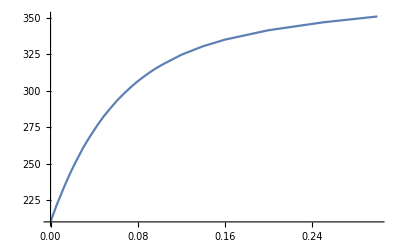

```mathematica
Plot[PLFUN[x,datax][[1]],{x,0,0.3}]
```

```mathematica
ApplyStrainComputeSigmaDep[epst_,epsp_,young_,nu_,sig0_]:=Block[{an,fn,sigy,invQ,G,K,lambda,mu,trialstress,Ce,sigsol,sxx,syy,sxy,dlambda,epse,Q,R,Ctc,asol,fb,ab,sigb,n,fc,Δλ,sigc,ac,r,λt,sigt,newsig,counter,tol=0.000001,res,diff,dads},
If[planestress==True,
Ce=young/(1-nu^2){{1,nu,0},{nu,1,0},{0,0,(1-nu)/2}};
,
Ce=young/((1+nu)(1-2nu) ){{1-nu,nu,0},{nu,1-nu,0},{0,0,(1-2nu)/2}};
];
trialstress=Ce.(epst-epsp);
(*Print["trialstress = ",trialstress];*)

(*{sigy,H}=PLFUN[Norm[epsp],datax];*)
sigy=sig0;
(*Print["trialstress = ",trialstress];
Print["F[trialstress,sigy] = ",F[trialstress,sigy]];*)
If[F[trialstress,sigy]>0,
sigb=trialstress;
n=10;
res=1;
counter=0.;
fb=F[sigb,sigy];
ab=a[sigb];
Δλ=fb/(ab.Ce.ab);
sigc=sigb-Δλ Ce.ab;
While[res≥tol &&counter<30,

fc=F[sigc,sigy];
ac=a[sigc];
r=sigc-(sigb-Δλ Ce.ac);
dads=dadsig[sigc];
Q=(IdentityMatrix[3]+Δλ Ce.dads);
invQ=Inverse[Q];
λt=(fc - ac.invQ.r)/(ac.invQ.Ce.ac);
sigt=-invQ.r - λt invQ.Ce.ac;
newsig=sigc+sigt;
fn=F[newsig,sigy];
an=a[newsig];
(*Δλ=fb/(ab.Ce.ab);*)
Δλ+=fn/(an.Ce.an);
diff=newsig-sigc;
res=Norm[diff];
(*Print["res = ",res];*)
sigc=newsig;
counter++;
];
sigsol=sigc;
asol=a[sigsol];
epse=Inverse[Ce].sigsol;
dlambda=(a[sigsol].Ce.(epst-epse))/(a[sigsol].Ce.a[sigsol]);
Q=(IdentityMatrix[3]+dlambda Ce.dadsig[sigsol]);
invQ=Inverse[Q];
R=invQ.Ce;
Ctc= R-1/(asol.R.asol) Outer[Times,R.asol,R.asol];

(*Inconsistent Tangent*)
(*Ctc = Ce-1/(asol.Ce.asol) Outer[Times,Ce.asol,Ce.asol];*)
(*Print["plastic"];*)
(*Print["epse = ",epse];*)
,
sigsol=trialstress;
epse=Inverse[Ce].sigsol;
Ctc=Ce;
(*Print["elastic"];*)
];
If[diverge==True,
Ctc=Ce;
];
{sigsol,Ctc,epse}

]
```

```mathematica
CoumpteStrain[gradprevsol_]:=Block[{dudx,dudy,dvdx,dvdy,gradu,strain,ex,ey,exy,ux,uy,kk},
(*Print["gradprevsol = ",gradprevsol];*)
{dudx,dudy,dvdx,dvdy}=gradprevsol;
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
{ex,ey,exy}
]
```

```mathematica
(*Calcula funçoes de forma 1D*)
ComputeShape[order_,var_]:=Block[{npoints},
npoints=order+1;
tab3[i_,n_]:=Table[If[j==i,1,0],{j,1,n}];
poli3[j_,n_]:=Table[{-1+2 (i-1)/(n-1),tab3[j,n][[i]]},{i,1,n}];
ListPoli[n_]:=Table[InterpolatingPolynomial[poli3[i,n],var],{i,1,n}];
ListPoli[npoints]
]
```

```mathematica
(*Encontra todos os ids e coordenadas entre os ids especificados*)
FindLineElemens[id1_,id2_,nnodes_,order_]:=Block[{h1,h2,allids,Flag,A,B,tol,i,ids,nodesvec,linenodes,temp1,temp2,elsvec,idsvec,nodes,newout,norm},
A=nnodes[[id1]];
B=nnodes[[id2]];
tol=10^-3;
linenodes={};
ids={};
nodesvec={};
elsvec={};
Flag=True;
h1=Sqrt[A[[1]]A[[1]]+A[[2]]A[[2]]];
h2=Sqrt[B[[1]]B[[1]]+B[[2]]B[[2]]];
For[i=1,i≤Length[nnodes],i++,
(*Vertical Line*)
If[Abs[A[[1]]-B[[1]]]<tol && Abs[nnodes[[i]][[1]]-A[[1]]]<tol,
If[Between[nnodes[[i]][[2]],{{A[[2]],B[[2]]},{B[[2]],A[[2]]}}],
AppendTo[linenodes,{nnodes[[i]],i}];
];
Flag=False;
,
(*Horizontal Line*)
If[Abs[A[[2]]-B[[2]]]<tol&& Abs[nnodes[[i]][[2]]-A[[2]]]<tol,
If[Between[nnodes[[i]][[1]],{{A[[1]],B[[1]]},{B[[1]],A[[1]]}}],
AppendTo[linenodes,{nnodes[[i]],i}];

];
Flag=False;
,
norm=Norm[nnodes[[i]]];
If[(Abs[norm-h1])<tol&&Abs[norm-h2]<tol  &&Flag≠False,
AppendTo[linenodes,{nnodes[[i]],i}];
 ];
];
];
];
newout=Transpose[SortBy[linenodes,Smaller]];
allids=newout[[2]];
nodes={};
ids={};
idsvec={};
nodesvec={};
Table[
AppendTo[nodes,newout[[1,i]]];
AppendTo[ids,newout[[2,i]]];
If[Length[ids]==order+1,
AppendTo[nodesvec,nodes];
AppendTo[idsvec,ids];
temp1=ids[[order+1]];
temp2=nodes[[order+1]];
nodes={};
ids={};
AppendTo[ids,temp1];
AppendTo[nodes,temp2];
];
,{i,1,Length[linenodes]}];
{nodesvec,idsvec,allids}
];
```

```mathematica
(*Aplica condição de contorno de dirichlet em uma linha definida por dois ids*)
ContributeLineDirichlet[EK_,EF_,nodes_,id1_,id2_,ek_,ef_,order_]:=Block[{nodevec,idsvec,x1,x2,y1,y2,Ef=EF,Ek=EK,els,ids,el,i,shapes,xx,J,xi,xix,w,integralxi1,vecPtosPesos,co,newco,j,k},
{nodevec,idsvec,ids}=FindLineElemens[id1,id2,nodes,order];
idsd2=ids;
el=Length[ids];
For[i=1,i≤el,i++,
For[j=1,j≤2,j++,
For[k=1,k≤2,k++,
Ek[[2ids[[i]] +j-2,2ids[[i]]+k-2 ]]*=ek[[j,k]];
];
Ef[[2ids[[i]] +j-2]]*=ef[[j]];
];
];
{Ek,Ef}
];
```

```mathematica
ComputeNormals[pt_]:=Block[{lines,x,delta,intdata,R=100,normal,v},
Clear[r];
rr[x_]=-x/(√(R^2-0.999999999999999 x^2));

pervec[v_]:={-v[[2]]/Norm[v],v[[1]]/Norm[v]};
lines=rr[pt[[1]]](x-pt[[1]])+ pt[[2]];
delta=10^-8;
normal=({pt[[1]]+delta,lines/.x->pt[[1]]+delta}-{pt[[1]],lines/.x->pt[[1]]})/Norm[({pt[[1]]+delta,lines/.x->pt[[1]]+delta}-{pt[[1]],lines/.x->pt[[1]]})];
pervec[normal]
]
```

```mathematica
(*Calcula a normal*)
ComputeNormalDirection[p1_,p2_]:=Block[{cos,sin},
cos=(p1[[1]]-p2[[1]])/Sqrt[(p1[[1]]-p2[[1]])^2 +(p1[[2]]-p2[[2]])^2];
sin=(p1[[2]]-p2[[2]])/Sqrt[(p1[[1]]-p2[[1]])^2 +(p1[[2]]-p2[[2]])^2];
{-sin,cos}
];
(*ComputeNormals[data_]:=Block[{lines,x,delta,normals},
rr[x_,{{x1_,y1_},{x2_,y2_},{x3_,y3_}}]:=-(2 x (-x2 y1+x3 y1+x1 y2-x3 y2-x1 y3+x2 y3))/((-x1+x2) (x2-x3) (-x1+x3))-(x2^2 y1-x3^2 y1-x1^2 y2+x3^2 y2+x1^2 y3-x2^2 y3)/((x1-x2) (x1-x3) (x2-x3));
lines=Table[(rr[data[[i,1]],data])(x-data[[i,1]])+data[[i,2]],{i,1,3}];
delta=10^-6;
normals=Table[({data[[i,1]]+delta,lines[[i]]/.x->(data[[i,1]]+delta) }-{data[[i,1]],lines[[i]]/.x->(data[[i,1]])})/Norm[{data[[i,1]]+delta,lines[[i]]/.x->(data[[i,1]]+delta) }-{data[[i,1]],lines[[i]]/.x->(data[[i,1]])}],{i,1,3}];
pervec[v_]:={-v[[2]]/Norm[v],v[[1]]/Norm[v]};
Table[pervec[normals[[i]]],{i,1,3}]
]*)

(*Calcula o vetor de cargas considerando a condição de contorno de Newmann*)
ContributeLineNewmanPressure[EF_,fx_,nodes_,order_,id1_,id2_]:=Block[{vecnodes,idsvec,ids,normal,coordinates,temp=0,co,el,i,shapes,xi,x0,y0,xf,yf,h,cos,sin,vertOrHor,x,J,vecPtosPesos,xix,w,integral,Ef=EF},
sumx=0.;
sumy=0.;
{vecnodes,idsvec,ids}=FindLineElemens[id1,id2,nodes,order];
vecdata=vecnodes;
(*Print["id1 = ",id1];
Print["id2 = ",id2];
Print["vecnodes = ",vecnodes];*)
el=Length[vecnodes];
shapes=ComputeShape[order,xi];
For[i=1,i≤el,i++,
coordinates=Table[0,{order+1}];
co=vecnodes[[i]];
x0=co[[1,1]];
xf=co[[Length[co],1]];
y0=co[[1,2]];
yf=co[[Length[co],2]];
h=Sqrt[(xf-x0)^2 +(yf-y0)^2];
cos=(xf-x0)/h;
sin=(yf-y0)/h;
temp=0;
Table[
coordinates[[k]]=temp;
temp+=h/order;
,{k,1,order+1}
];
(*teste=ComputeNormals[co];*)
x=Sum[shapes[[i]] coordinates[[i]],{i,1,order+1}];
J=D[x,xi];
vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integral=Table[Sum[((fx[co[[j]]]shapes[[j]]J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}];
Table[
normal=ComputeNormals[vecnodes[[i]][[j]]];
Ef[[ idsvec[[i,j]] 2-1]]+=integral[[j]]normal[[1]];
Ef[[ idsvec[[i,j]] 2]]+=integral[[j]]normal[[2]];
,{j,1,order+1}];
];
Ef
];
```

```mathematica
sumx=0.;
sumy=0.;
```

```mathematica
(*Calcula o vetor de cargas considerando a condição de contorno de Newmann*)
ContributeLineNewman[EF_,fx_,nodes_,order_,id1_,id2_]:=Block[{vecnodes,idsvec,ids,normal,coordinates,temp=0,co,el,i,shapes,xi,x0,y0,xf,yf,h,cos,sin,vertOrHor,x,J,vecPtosPesos,xix,w,integral,Ef=EF},
sumx=0.;
sumy=0.;
{vecnodes,idsvec,ids}=FindLineElemens[id1,id2,nodes,order];
vecdata=vecnodes;
(*Print["id1 = ",id1];
Print["id2 = ",id2];
Print["vecnodes = ",vecnodes];*)
el=Length[vecnodes];
shapes=ComputeShape[order,xi];
For[i=1,i≤el,i++,
coordinates=Table[0,{order+1}];
co=vecnodes[[i]];
x0=co[[1,1]];
xf=co[[Length[co],1]];
y0=co[[1,2]];
yf=co[[Length[co],2]];
h=Sqrt[(xf-x0)^2 +(yf-y0)^2];
cos=(xf-x0)/h;
sin=(yf-y0)/h;
temp=0;
Table[
coordinates[[k]]=temp;
temp+=h/order;
,{k,1,order+1}
];
(*teste=ComputeNormals[co];*)
x=Sum[shapes[[i]] coordinates[[i]],{i,1,order+1}];
J=D[x,xi];
vecPtosPesos=GaussianQuadratureWeights[order+1,-1,1];
{xix,w}=Transpose[vecPtosPesos];
integral=Table[Sum[((fx[co[[j]]]shapes[[j]]J)/.xi->xix[[i]]) w[[i]],{i,1,Length[xix]}],{j,1,Length[shapes]}];
Table[
If[j≠order+1,
normal=ComputeNormalDirection[vecnodes[[i]][[j]],vecnodes[[i]][[j+1]]];
];
Ef[[ idsvec[[i,j]] 2-1]]+=integral[[j]]normal[[1]];
Ef[[ idsvec[[i,j]] 2]]+=integral[[j]]normal[[2]];


,{j,1,order+1}];
];
Ef
];
```

```mathematica
(*Dada uma coordenada de nó encontra o correspondente id*)
FindIds[nodes_,coords_]:=Block[{nodestofind=Nearest[nodes,coords][[All,1]]},Flatten[Position[nodes,Alternatives@@nodestofind]]]
```

```mathematica
(*Calcula a solução e a derivada definida em cada elemento*)
ComputeSol[topol_,coords_,order_,coefs_,eltype_]:=Block[{X,InvJ,GradPhi,GradPsi,nels,dsol,xa,xb,k=0,i,phi,sol,phisz,j,xx,J,co,h,x=0,psis,id,y=0,xi,eta,Jac,DetJac,kk},
{psis,GradPsi}=Compute2DShape[order,eltype];
nels=Length[topol];
sol=Table[0,{nels},{2}];
X=Table[0,{nels},{2}];
dsol=Table[0,{nels},{4}];
Table[
x=0.;
y=0.;
kk=Length[psis];
Table[
id=topol[[i,j]];
x+=coords[[id,1]] psis[[j]];
y+=coords[[id,2]] psis[[j]];
,{j,1,kk}];
Jac={{D[x,xi],D[y,xi]},{D[x,eta],D[y,eta]}};
DetJac=Det[Jac];
InvJ=Inverse[Jac];
GradPhi=InvJ.GradPsi;
Table[
id=topol[[i,j]];
sol[[i,1]]+=(psis[[j]] coefs[[2 id-1]] );
sol[[i,2]]+=(psis[[j]] coefs[[2id]] );
(*(*duxdx*)
dsol[[i,1]]+=(GradPhi[[1,j]]coefs[[2 id-1]] );
(*duxdy*)
dsol[[i,2]]+=(GradPhi[[2,j]] coefs[[2id-1]] );
(*duydx*)
dsol[[i,3]]+=(GradPhi[[1,j]]coefs[[2id]] );
(*duydy*)
dsol[[i,4]]+=(GradPhi[[2,j]] coefs[[2id]] );
*)

(*dudx*)
dsol[[i,1]]+=(GradPhi[[1,j]]coefs[[2 id-1]] );
(*dvdx*)
dsol[[i,2]]+=(GradPhi[[2,j]] coefs[[2id-1]] );
(*dudy*)
dsol[[i,3]]+=(GradPhi[[1,j]]coefs[[2id]] );
(*dvdy*)
dsol[[i,4]]+=(GradPhi[[2,j]] coefs[[2id]] );

,
{j,1,kk}];
X[[i,1]]=x;
X[[i,2]]=y;
,{i,1,nels}];
{sol,dsol,X}
]
```

```mathematica
(*Função de auxílio ao pós-processamento*)
computesollist[X_,sols_,sx_]:=Block[{refine,sollists,v,x,y,s,sollist},
sollists={};
refine=1/3.;
v=Table[{xi,eta},{xi,0,1,refine},{eta,1-xi,0,-refine}];
sollists=Table[0,{Length[X]}];
Table[
xx[xii_,etaa_]:=X[[i,1]]/.{xi->xii,eta->etaa};
yy[xii_,etaa_]:=X[[i,2]]/.{xi->xii,eta->etaa};
Sol[xii_,etaa_]:=sols[[i,sx]]/.{xi->xii,eta->etaa};
x=xx[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
y=yy[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
s=Sol[#1,#2]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=ParallelTable[{x[[i]],y[[i]],s[[i]]},{i,1,Length[s]}];
sollists[[i]]=sollist;
,{i,1,Length[X]}];
sollists
]
```

```mathematica
(*Dada a matriz de rigidez e o vetor de carga globais, aplica condição de contorno definida em nós*)
ApplyNodeBC[Kglob_,Fglob_,node_,type_,ek_,ef_]:=Block[{position,i,j,kglob=Kglob,fglob=Fglob},

If[type≠0&&type≠1 && type≠2,Print["Unknown type. Specify 0 for Dirichlet, 1 for Newman or 2 for Mixed."]];
position=node 2-1;
If[type==0,
(*Dirichlet - Specified Solution *)
For[i=1,i≤2,i++,
For[j=1,j≤2,j++,
kglob[[position+i-1,position+j-1]]*=ek[[i,j]];
];
fglob[[position+i-1]]=ef[[i]];
];
];
If[type==1,
For[i=1,i≤2,i++,
fglob[[position+i-1]]+=ef[[i]];
];
];
{kglob,fglob}
]
```

```mathematica
(*Dada a matriz de rigidez e o vetor de carga globais, aplica condição de contorno definida em nós*)
FindBig[Kglob_]:=Block[{position,i,j,kglob=Kglob,k},

For[i=1,i≤Length[kglob],i++,
For[j=1,j≤Length[kglob],j++,
If[kglob[[i,j]]> 10^12,

For[k=1,k≤Length[kglob],k++,
kglob[[i,k]]=0;
kglob[[k,j]]=0;
];
kglob[[i,j]]=1.;
];
];

];
kglob
]
```

```mathematica
postproc[X_,sols_]:=Block[{refine,sollists,v,x,y,postvar,sollist},
sollists={};
If[eltype==1,
refine=0.25;
v=Table[{xi,eta},{xi,-1,1,refine},{eta,-1,1,refine}];
,
refine=1/3.;
v=Table[{xi,eta},{xi,0,1,refine},{eta,1-xi,0,-refine}];
];
sollists=Table[0,{Length[X]}];
pt[xii_,etaa_,var_]:=var/.{xi->xii,eta->etaa};
Sol[xii_,etaa_,var_]:=var/.{xi->xii,eta->etaa};
Table[
x=pt[#1,#2,X[[i]]]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
postvar=Sol[#1,#2,sols[[i]]]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=Table[{x[[1,k]],x[[2,k]],postvar[[k]]},{k,1,Length[postvar]}];
sollists[[i]]=sollist;
,{i,1,Length[X]}];
sollists
]
```

```mathematica
postproc2[X_,sols_]:=Block[{refine,sollists,v,x,y,postvar,sollist},
sollists={};
If[eltype==1,
refine=0.25;
v=Table[{xi,eta},{xi,-1,1,refine},{eta,-1,1,refine}];
,
refine=1/3.;
v=Table[{xi,eta},{xi,0,1,refine},{eta,1-xi,0,-refine}];
];
sollists=Table[0,{Length[X]}];
pt[xii_,etaa_,var_]:=var/.{xi->xii,eta->etaa};
Sol[xii_,etaa_,var_]:=var/.{xi->xii,eta->etaa};
Table[
x=pt[#1,#2,X[[i]]]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
postvar=Sol[#1,#2,sols[[i]]]&[Transpose[Flatten[v,1]][[1]],Transpose[Flatten[v,1]][[2]]];
sollist=Table[{x[[1,k]],x[[2,k]],sols[[k]]},{k,1,Length[sols]}];
sollists[[i]]=sollist;
,{i,1,Length[X]}];
sollists
]
```

```mathematica
ComputeStress[dsol_,young_,nu_]:=Block[{I1,stressz,sigxy,sigx,sigy,sigz,strain,gradu,lambda=young nu/((1+nu)(1-2 nu)),mu=young/(2(1+nu)),dudx,dudy,dvdx,dvdy,i,eps,stress,ex,ey,exy,C,J2,sig,SZ=szz},

strain=Table[0,{Length[dsol]}];
stress=Table[0,{Length[dsol]}];
J2=Table[0,{Length[dsol]}];
I1=Table[0,{Length[dsol]}];
stressz=Table[0,{Length[dsol]}];
For[i=1,i≤Length[dsol],i++,

{dudx,dudy,dvdx,dvdy}=dsol[[i]];
ex=dudx;
ey=dvdy;
exy=(dudy+dvdx);
strain={ex,ey,exy};

If[planestress==True,
C=young/(1-nu^2){{1,nu,0},{nu,1,0},{0,0,(1-nu)/2}};
sz[sx_,sy_]:=0;
,
C=young/((1+nu)(1-2nu) ){{1-nu,nu,0},{nu,1-nu,0},{0,0,(1-2nu)/2}};
(*sz[sx_,sy_]:=nu((sx+sy)- (Sh+Sh))+SZ ;*)
sz[sx_,sy_]:=nu(sx+sy) ;
];
stress[[i]]=C.strain;
sig=C.strain;
sigxy=sig[[3]];
sigx=sig[[1]];
sigy=sig[[2]];
sigz=sz[sigx,sigy];
stressz[[i]]=sigz;
I1[[i]]=sigx+sigy+sigz;
J2[[i]]=1/3.(sigx^2+3. sigxy^2+sigy^2-sigy sigz+sigz^2-sigx (sigy+sigz));

];
{stress,strain,stressz,J2,I1}
];
```

```mathematica
ContributeKt[data_,weight_,order_,gradprevsol_]:=Block[{fu,InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ek,i,j,x,y,C},
f[x_]:=0;
{psi,GradPsi,Jac,x,y}=data;
nnodes=Length[psi] ;
DetJ=Jac[[1,1]] Jac[[2,2]]-Jac[[2,1]] Jac[[1,2]];
InvJac={{Jac[[2,2]],-Jac[[1,2]]},{-Jac[[2,1]],Jac[[1,1]]}}/DetJ;
GradPhi=InvJac.GradPsi;
wpLocal=weight  DetJ;
(*If[planestress==True,
C=young/(1-nu^2){{1,nu,0},{nu,1,0},{0,0,(1-nu)/2}};
,
C=young/((1+nu)(1-2nu) ){{1-nu,nu,0},{nu,1-nu,0},{0,0,(1-2nu)/2}};
]; *)
epst=CoumpteStrain[gradprevsol];
epsp=epspsolitern[[globalcounter]];
{sigsol,C,epse}=ApplyStrainComputeSigmaDep[epst,epsp,young,nu,sigy];
epspeint=epst-epse;
epspvec[[globalcounter]]=epspeint;
globalcounter++;

ek=Table[0,{nnodes 2},{nnodes 2}];
fu=-1;
Table[
Table[
ek[[2 i+fu,2j+fu]]+=( GradPhi[ [1,i]] C[[1,1]]  GradPhi[[1,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[2,j]])wpLocal  ;
ek[[2 i+fu,2j+1+fu]]+=( GradPhi[[1,i]] C[[1,2]]  GradPhi[[2,j]]+GradPhi[[2,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
ek[[2 i+1+fu,2j+fu]]+=( GradPhi[[2,i]] C[[1,2]]  GradPhi[[1,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[2,j]])wpLocal ;
ek[[2 i+1+fu,2j+1+fu]]+=( GradPhi[[2,i]] C[[2,2]]  GradPhi[[2,j]]+GradPhi[[1,i]]C[[3,3]]GradPhi[[1,j]])wpLocal ;
,{j,1, nnodes}];
,{i,1, nnodes}];

ek
]
```

```mathematica
ContributeFInt[data_,weight_,order_,gradprevsol_]:=Block[{f,InvJac,GradPsi,nnodes,Jac,GradPhi,DetJ,wpLocal,psi,ef,x,y,i,j},

f[x_]:=0;
{psi,GradPsi,Jac,x,y}=data;
nnodes=Length[psi] ;
DetJ=Jac[[1,1]] Jac[[2,2]]-Jac[[2,1]] Jac[[1,2]];
InvJac={{Jac[[2,2]],-Jac[[1,2]]},{-Jac[[2,1]],Jac[[1,1]]}}/DetJ;
GradPhi=InvJac.GradPsi;
wpLocal=weight  DetJ;

epst=CoumpteStrain[gradprevsol];
epsp=epspsolitern[[globalcounter]];
{sigsol,C,epse}=ApplyStrainComputeSigmaDep[epst,epsp,young,nu,sigy];
epspeint=epst-epse;
epspvec[[globalcounter]]=epspeint;
globalcounter++;
AppendTo[epsppost,{x,y,epsp}];
AppendTo[stressppost,{x,y,sigsol}];
ef=Table[0,{nnodes 2}];
Table[
ef[[2 i-1]] += psi[[i]]wpLocal f[x]+(sigsol[[1]] GradPhi[[1,i]]+sigsol[[3]] GradPhi[[2,i]])wpLocal;
ef[[2 i]]+=psi[[i]] wpLocal f[x]+(sigsol[[3]] GradPhi[[1,i]]+sigsol[[2]] GradPhi[[2,i]])wpLocal;
,{i,1, nnodes}];
ef
]
```

```mathematica
(*Calcula a matriz de rigidez de cada elemento*)
CalcElementFInt[order_,elcoords_,eltype_,gradprevsol_]:=Block[{nnodes,ek,ef,intrule,psis,GradPsi,xi,eta,data,w,npts,sigsol,C,epse,epst,epsp,epspeint,Jac,x,y,psi},

intrule=IntegrationRule[order,eltype];
{psis,GradPsi}=Compute2DShape[order,eltype];
nnodes=Length[psis];
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

npts=Length[intrule];
Table[
{xi,eta,w}=intrule[[i]];
data=ComputeData[elcoords,psis,GradPsi];
(*data={psi,GradPsi,Jac,x,y};*)
(*epst=CoumpteStrain[gradprevsol];
epsp=epspsolitern[[globalcounter]];
{sigsol,C,epse}=ApplyStrainComputeSigmaDep[epst,epsp,young,nu,sigy];
epspeint=epst-epse;
epspvec[[globalcounter]]=epspeint;
globalcounter++;*)
ef+=ContributeFInt[data,w,order,gradprevsol];
,{i,1,npts}];
ef
]
```

```mathematica
(*Realiza a montagem da matriz de rigidez global*)
AssembleGlobalFint[allcoords_,nnodes_,topol_,order_,eltype_,gradprevsol_]:=Block[{nels,rows,sz,Fglob,co,Fe,fu,rowglob},
nels=Length[allcoords];
rows=Length[allcoords[[1]]] ;
sz= 2 Length[nnodes];
Fglob=Table[0,{sz}];
Table[
co=allcoords[[k]]//N;
Fe=CalcElementFInt[order,co,eltype,gradprevsol[[k]]];
fu=-1;
Table[
rowglob=topol[[k,i]];
Fglob[[2rowglob+fu]]+=Fe[[2 i+fu]];
Fglob[[2rowglob]]+=Fe[[2 i]];
,{i,1,rows}];
,{k,1,nels}];
Fglob
]
```

```mathematica
(*Calcula a matriz de rigidez de cada elemento*)
CalcElementStiff[order_,elcoords_,eltype_,gradprevsol_]:=Block[{nnodes,ek,ef,intrule,psis,GradPsi,xi,eta,data,w,npts,prevsolinternal},


intrule=IntegrationRule[order,eltype];
{psis,GradPsi}=Compute2DShape[order,eltype];
nnodes=Length[psis];
ek=Table[0,{nnodes 2},{nnodes 2}];
ef=Table[0,{nnodes 2}];

npts=Length[intrule];
Table[
{xi,eta,w}=intrule[[i]];
data=ComputeData[elcoords,psis,GradPsi];
ek+=ContributeKt[data,w,order,gradprevsol];
,{i,1,npts}
];
ek
]
```

```mathematica
(*Realiza a montagem da matriz de rigidez global*)
AssembleGlobalKt[allcoords_,nnodes_,topol_,order_,eltype_,gradprevsol_]:=Block[{nels,rows,sz,cols,Kglob,Fglob,co,Ke,Fe,fu,rowglob,colglob},
nels=Length[allcoords];
rows=Length[allcoords[[1]]] ;
sz= 2 Length[nnodes];
cols=rows;
Kglob=Table[0,{ sz},{ sz}];
Fglob=Table[0,{sz}];
Table[
co=allcoords[[k]]//N;
Ke=CalcElementStiff[order,co,eltype,gradprevsol[[k]]];
fu=-1;
Table[
rowglob=topol[[k,i]];
Table[
colglob=topol[[k,j]];
Kglob[[2 rowglob+fu,2 colglob+fu]]+=Ke[[2 i+fu,2 j+fu]];
Kglob[[2rowglob+fu,2colglob+1+fu]]+=Ke[[2i+fu,2j+1+fu]];
Kglob[[2rowglob+1+fu,2colglob+fu]]+=Ke[[2i+1+fu,2j+fu]];
Kglob[[2rowglob+1+fu,2colglob+1+fu]]+=Ke[[2i+1+fu,2j+1+fu]];
,{j,1,cols}];
,{i,1,rows}];
,{k,1,nels}];
Kglob
]
```

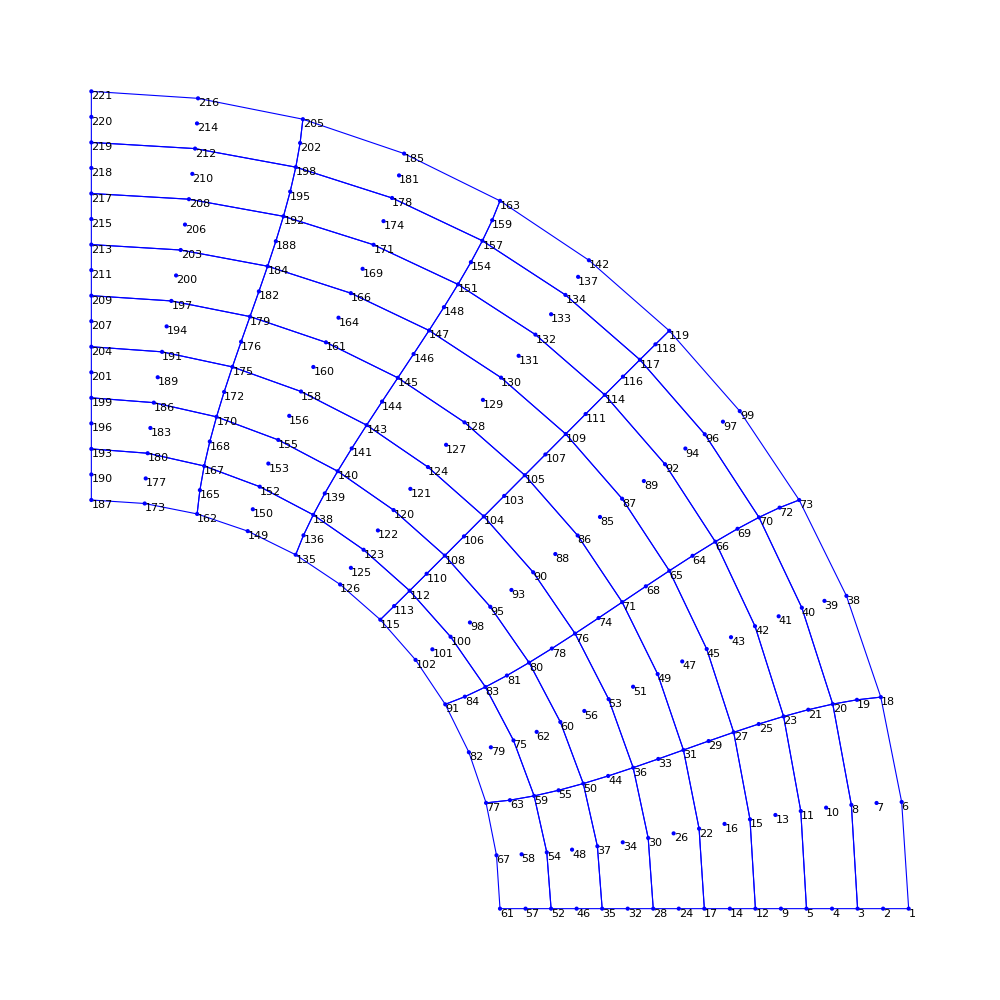

```mathematica
pack=Developer`ToPackedArray;
topol=pack@Transpose@Drop[Transpose@Import["C:\\Users\\diogo\\Dropbox\\poco-paper-FEM\\elementsring.txt","Table"],1];
nnodesAll=Import["C:\\Users\\diogo\\Dropbox\\poco-paper-FEM\\nodesring.txt","Table"];
nnodes=pack@N[nnodesAll[[All,{2,3}]]];
allcoords=ParallelTable[nnodes[[topol[[i]][[j]]]],{i,1,Length[topol]},{j,1,9}];
(*edges are straight*)
meshVis1=Graphics[{FaceForm[],EdgeForm[Blue],GraphicsComplex[nnodes,Polygon[topol[[All,{1,5,2,6,3,7,4,8}]]]]}];
nodeVis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nnodes],{Blue,Point[nnodes]}}];
mesh=Show[meshVis1,nodeVis,ImageSize->1000]
```

```mathematica
100/17.
```

5.88235

```mathematica
R=100;
RF=200;
nodetofind={{R,0},{0,R}};
{hole1,hole2}=FindIds[nnodes,nodetofind]
nodetofind={{RF,0},{0,RF}};
{hole3,hole4}=FindIds[nnodes,nodetofind]

nodetofind={{R,0},{RF,0}};
{inferiorline1,inferiorline2}=FindIds[nnodes,nodetofind]
nodetofind={{0,R},{0,RF}};
{leftline1,leftline2}=FindIds[nnodes,nodetofind]
```

{61,187}

{1,221}

{1,61}

{187,221}

```mathematica
FindLineElemens[leftline1,leftline2,nnodes,order][[3]]
```

{187,190,193,196,199,201,204,207,209,211,213,215,217,218,219,220,221}

```mathematica
eltype=1;
order=2;
young=210000;
sigy=240;
nu=0.3;
globalcounter=1;
intrule=IntegrationRule[order,eltype];
npts=Length[intrule]; 
nglobalpts=Length[topol] npts;
epspvec=Table[0,{nglobalpts},{3}];
epspsolitern=Table[0,{nglobalpts},{3}];
epstvec=Table[0,{nglobalpts},{3}];
epstsolitern=Table[0,{nglobalpts},{3}];
dsols=Table[0,{nglobalpts},{4}];
un=Table[0,{Length[nnodes]2}];
epspsolitern=Table[0,{nglobalpts},{3}];



steps=2.;
sf=192.09;
lambda=0.05;
post2={};
(*lambda=0.4;*)
un=Table[0,{Length[nnodes]2}];
diverge=False;
planestress=False;

(*un=sol;*)
(*Print["un1 = ",Chop[un,10^-6]];*)
solss={};
outerdisplace={};
plasticsols={};
{sols,dsols,X}=ComputeSol[topol,nnodes,order,un,eltype];
epspsolu={};
stresssolu={};
diverge=False;
For[i=1,i≤20,i++,
Print[" ---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = ", i ];
resnorm=1.;
counter=1;
flag=False;
globalcounter=1;
KE=AssembleGlobalKt[allcoords,nnodes,topol,order,eltype,dsols];
FINT=Table[0,{Length[KE]}];
{KE,FINT}=ContributeLineDirichlet[KE,FINT,nnodes,leftline2,leftline1,{{10^12,1},{1,1}},{0,0},order];
{KE,FINT}=ContributeLineDirichlet[KE,FINT,nnodes,inferiorline2,inferiorline1,{{1,1},{1,10^12}},{0,0},order];

FE=Table[0,{Length[FINT]}];
f[pt_]:=lambda sf ;
FE=ContributeLineNewmanPressure[FE,f,nnodes,order,hole2,hole1];

While[resnorm>10^-3&& counter≤60,

(*If[diverge==True,*)
If[i==18,
Print["Divergente"];
diverge=True;
globalcounter=1;
KE=AssembleGlobalKt[allcoords,nnodes,topol,order,eltype,dsols];
{KE,FINT}=ContributeLineDirichlet[KE,FINT,nnodes,leftline2,leftline1,{{10^12,1},{1,1}},{0,0},order];
{KE,FINT}=ContributeLineDirichlet[KE,FINT,nnodes,inferiorline2,inferiorline1,{{1,1},{1,10^12}},{0,0},order];
];

epsppost={};
stressppost={};

(*globalcounter=1;
KE=AssembleGlobalKt[allcoords,nnodes,topol,order,eltype,dsols];
FINT=Table[0,{Length[KE]}];
{KE,FINT}=ContributeLineDirichlet[KE,FINT,nnodes,leftline2,leftline1,{{10^12,1},{1,1}},{0,0},order];
{KE,FINT}=ContributeLineDirichlet[KE,FINT,nnodes,inferiorline2,inferiorline1,{{1,1},{1,10^12}},{0,0},order];*)


globalcounter=1;
FINT=AssembleGlobalFint[allcoords,nnodes,topol,order,eltype,dsols];


r=FINT- FE;

(*Print["FE= ",Chop[FE,10^-3]];
Print["FINT= ",Chop[FINT,10^-3]];
Print["r= ",Chop[r,10^-3]];*)

du=LinearSolve[KE,-r,Method->"Banded"];
un+=du;

{KE,r}=ContributeLineDirichlet[KE,r,nnodes,leftline2,leftline1,{{1,1},{1,1}},{0,0},order];
{KE,r}=ContributeLineDirichlet[KE,r,nnodes,inferiorline2,inferiorline1,{{1,1},{1,1}},{0,0},order];
resnorm=Norm[r]/Norm[FE];

(*resnorm=Norm[du];*)
If[resnorm>dun,diverge=True];

{sols,dsols,X}=ComputeSol[topol,nnodes,order,un,eltype];

Print["counter  = ",counter , " | Norm[FE] = ",Norm[FE], " | Norm[FINT] = ",Norm[FINT],"| Norm[r] = ",Norm[r], "  | f = ",lambda sf , "| Norm[du] = ",Norm[du]," | Norm[r]/Norm[FE] = ",Norm[r]/Norm[FE] ];
counter++;
];

(*dados para pos -processamento*)
AppendTo[stresssolu,stressppost];
AppendTo[epspsolu,epsppost];
AppendTo[solss,un];
AppendTo[outerdisplace,{un[[1]], lambda sf}];
AppendTo[plasticsols,epspvec];

(*Atualiza variável de estado plástica no passo convergido*)
epspsolitern=epspvec;
lambda+=0.05;

(*Reseta solução e derivadas*)
dsols=Table[0,{nglobalpts},{4}];
un=Table[0,{Length[nnodes]2}];
];
```

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 1

counter  = 1 | Norm[FE] = 453.934 | Norm[FINT] = 0.| Norm[r] = 450.07  | f = 9.6045| Norm[du] = 0.100714 | Norm[r]/Norm[FE] = 0.991489

counter  = 2 | Norm[FE] = 453.934 | Norm[FINT] = 583.148| Norm[r] = 4.24807×10^-11  | f = 9.6045| Norm[du] = 7.89933×10^-15 | Norm[r]/Norm[FE] = 9.35836×10^-14

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 2

counter  = 1 | Norm[FE] = 907.867 | Norm[FINT] = 2.01676×10^-13| Norm[r] = 900.14  | f = 19.209| Norm[du] = 0.201429 | Norm[r]/Norm[FE] = 0.991489

counter  = 2 | Norm[FE] = 907.867 | Norm[FINT] = 1166.3| Norm[r] = 8.58234×10^-11  | f = 19.209| Norm[du] = 1.56724×10^-14 | Norm[r]/Norm[FE] = 9.4533×10^-14

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 3

counter  = 1 | Norm[FE] = 1361.8 | Norm[FINT] = 4.32166×10^-13| Norm[r] = 1350.21  | f = 28.8135| Norm[du] = 0.302143 | Norm[r]/Norm[FE] = 0.991489

counter  = 2 | Norm[FE] = 1361.8 | Norm[FINT] = 1749.44| Norm[r] = 1.38193×10^-10  | f = 28.8135| Norm[du] = 2.34499×10^-14 | Norm[r]/Norm[FE] = 1.01478×10^-13

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 4

counter  = 1 | Norm[FE] = 1815.73 | Norm[FINT] = 7.42333×10^-13| Norm[r] = 1800.28  | f = 38.418| Norm[du] = 0.402858 | Norm[r]/Norm[FE] = 0.991489

counter  = 2 | Norm[FE] = 1815.73 | Norm[FINT] = 2332.59| Norm[r] = 1.7176×10^-10  | f = 38.418| Norm[du] = 3.15289×10^-14 | Norm[r]/Norm[FE] = 9.45955×10^-14

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 5

counter  = 1 | Norm[FE] = 2269.67 | Norm[FINT] = 1.18095×10^-12| Norm[r] = 2250.35  | f = 48.0225| Norm[du] = 0.503572 | Norm[r]/Norm[FE] = 0.991489

counter  = 2 | Norm[FE] = 2269.67 | Norm[FINT] = 2915.74| Norm[r] = 2.14991×10^-10  | f = 48.0225| Norm[du] = 3.93974×10^-14 | Norm[r]/Norm[FE] = 9.47234×10^-14

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 6

counter  = 1 | Norm[FE] = 2723.6 | Norm[FINT] = 1.52222×10^-12| Norm[r] = 2700.42  | f = 57.627| Norm[du] = 0.604287 | Norm[r]/Norm[FE] = 0.991489

counter  = 2 | Norm[FE] = 2723.6 | Norm[FINT] = 3498.89| Norm[r] = 2.7354×10^-10  | f = 57.627| Norm[du] = 4.68387×10^-14 | Norm[r]/Norm[FE] = 1.00433×10^-13

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 7

counter  = 1 | Norm[FE] = 3177.53 | Norm[FINT] = 1.8498×10^-12| Norm[r] = 3150.49  | f = 67.2315| Norm[du] = 0.705001 | Norm[r]/Norm[FE] = 0.991489

counter  = 2 | Norm[FE] = 3177.53 | Norm[FINT] = 4082.04| Norm[r] = 3.18242×10^-10  | f = 67.2315| Norm[du] = 5.48454×10^-14 | Norm[r]/Norm[FE] = 1.00154×10^-13

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 8

counter  = 1 | Norm[FE] = 3631.47 | Norm[FINT] = 2.51745×10^-12| Norm[r] = 3600.56  | f = 76.836| Norm[du] = 0.805716 | Norm[r]/Norm[FE] = 0.991489

counter  = 2 | Norm[FE] = 3631.47 | Norm[FINT] = 4665.19| Norm[r] = 3.42887×10^-10  | f = 76.836| Norm[du] = 6.30318×10^-14 | Norm[r]/Norm[FE] = 9.44211×10^-14

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 9

counter  = 1 | Norm[FE] = 4085.4 | Norm[FINT] = 3.31117×10^-12| Norm[r] = 4050.63  | f = 86.4405| Norm[du] = 0.90643 | Norm[r]/Norm[FE] = 0.991489

counter  = 2 | Norm[FE] = 4085.4 | Norm[FINT] = 5248.33| Norm[r] = 4.09311×10^-10  | f = 86.4405| Norm[du] = 7.16086×10^-14 | Norm[r]/Norm[FE] = 1.00189×10^-13

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 10

counter  = 1 | Norm[FE] = 4539.34 | Norm[FINT] = 3.98502×10^-12| Norm[r] = 4500.7  | f = 96.045| Norm[du] = 1.00714 | Norm[r]/Norm[FE] = 0.991489

counter  = 2 | Norm[FE] = 4539.34 | Norm[FINT] = 5831.48| Norm[r] = 4.21911×10^-10  | f = 96.045| Norm[du] = 7.92758×10^-14 | Norm[r]/Norm[FE] = 9.29457×10^-14

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 11

counter  = 1 | Norm[FE] = 4993.27 | Norm[FINT] = 4.43337×10^-12| Norm[r] = 4950.77  | f = 105.649| Norm[du] = 1.10786 | Norm[r]/Norm[FE] = 0.991489

counter  = 2 | Norm[FE] = 4993.27 | Norm[FINT] = 6408.76| Norm[r] = 16.047  | f = 105.649| Norm[du] = 0.000146145 | Norm[r]/Norm[FE] = 0.00321373

counter  = 3 | Norm[FE] = 4993.27 | Norm[FINT] = 6413.11| Norm[r] = 3.95988  | f = 105.649| Norm[du] = 0.0000360102 | Norm[r]/Norm[FE] = 0.000793043

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 12

counter  = 1 | Norm[FE] = 5447.2 | Norm[FINT] = 19.9833| Norm[r] = 5410.35  | f = 115.254| Norm[du] = 1.20872 | Norm[r]/Norm[FE] = 0.993234

counter  = 2 | Norm[FE] = 5447.2 | Norm[FINT] = 6717.88| Norm[r] = 532.409  | f = 115.254| Norm[du] = 0.00693196 | Norm[r]/Norm[FE] = 0.0977399

counter  = 3 | Norm[FE] = 5447.2 | Norm[FINT] = 6906.98| Norm[r] = 153.763  | f = 115.254| Norm[du] = 0.00221888 | Norm[r]/Norm[FE] = 0.0282279

counter  = 4 | Norm[FE] = 5447.2 | Norm[FINT] = 6965.18| Norm[r] = 52.5822  | f = 115.254| Norm[du] = 0.000777508 | Norm[r]/Norm[FE] = 0.00965306

counter  = 5 | Norm[FE] = 5447.2 | Norm[FINT] = 6985.16| Norm[r] = 18.8165  | f = 115.254| Norm[du] = 0.000273175 | Norm[r]/Norm[FE] = 0.00345435

counter  = 6 | Norm[FE] = 5447.2 | Norm[FINT] = 6992.17| Norm[r] = 6.90648  | f = 115.254| Norm[du] = 0.0000969665 | Norm[r]/Norm[FE] = 0.00126789

counter  = 7 | Norm[FE] = 5447.2 | Norm[FINT] = 6994.62| Norm[r] = 2.6817  | f = 115.254| Norm[du] = 0.0000351507 | Norm[r]/Norm[FE] = 0.000492308

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 13

counter  = 1 | Norm[FE] = 5901.14 | Norm[FINT] = 787.092| Norm[r] = 6420.03  | f = 124.859| Norm[du] = 1.31975 | Norm[r]/Norm[FE] = 1.08793

counter  = 2 | Norm[FE] = 5901.14 | Norm[FINT] = 7122.01| Norm[r] = 661.469  | f = 124.859| Norm[du] = 0.0163346 | Norm[r]/Norm[FE] = 0.112092

counter  = 3 | Norm[FE] = 5901.14 | Norm[FINT] = 7384.41| Norm[r] = 264.224  | f = 124.859| Norm[du] = 0.0058824 | Norm[r]/Norm[FE] = 0.0447751

counter  = 4 | Norm[FE] = 5901.14 | Norm[FINT] = 7488.28| Norm[r] = 108.393  | f = 124.859| Norm[du] = 0.00241473 | Norm[r]/Norm[FE] = 0.0183682

counter  = 5 | Norm[FE] = 5901.14 | Norm[FINT] = 7531.08| Norm[r] = 45.9073  | f = 124.859| Norm[du] = 0.00103272 | Norm[r]/Norm[FE] = 0.00777941

counter  = 6 | Norm[FE] = 5901.14 | Norm[FINT] = 7549.22| Norm[r] = 19.8276  | f = 124.859| Norm[du] = 0.000446008 | Norm[r]/Norm[FE] = 0.00335997

counter  = 7 | Norm[FE] = 5901.14 | Norm[FINT] = 7557.03| Norm[r] = 8.68024  | f = 124.859| Norm[du] = 0.000193925 | Norm[r]/Norm[FE] = 0.00147094

counter  = 8 | Norm[FE] = 5901.14 | Norm[FINT] = 7560.42| Norm[r] = 3.90131  | f = 124.859| Norm[du] = 0.0000851236 | Norm[r]/Norm[FE] = 0.000661112

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 14

counter  = 1 | Norm[FE] = 6355.07 | Norm[FINT] = 1868.92| Norm[r] = 7849.65  | f = 134.463| Norm[du] = 1.44679 | Norm[r]/Norm[FE] = 1.23518

counter  = 2 | Norm[FE] = 6355.07 | Norm[FINT] = 7684.4| Norm[r] = 632.678  | f = 134.463| Norm[du] = 0.0249119 | Norm[r]/Norm[FE] = 0.0995549

counter  = 3 | Norm[FE] = 6355.07 | Norm[FINT] = 7903.39| Norm[r] = 310.77  | f = 134.463| Norm[du] = 0.0111396 | Norm[r]/Norm[FE] = 0.0489011

counter  = 4 | Norm[FE] = 6355.07 | Norm[FINT] = 8014.28| Norm[r] = 157.902  | f = 134.463| Norm[du] = 0.00548576 | Norm[r]/Norm[FE] = 0.0248466

counter  = 5 | Norm[FE] = 6355.07 | Norm[FINT] = 8070.31| Norm[r] = 82.3  | f = 134.463| Norm[du] = 0.00278604 | Norm[r]/Norm[FE] = 0.0129503

counter  = 6 | Norm[FE] = 6355.07 | Norm[FINT] = 8099.11| Norm[r] = 43.3545  | f = 134.463| Norm[du] = 0.00144212 | Norm[r]/Norm[FE] = 0.00682203

counter  = 7 | Norm[FE] = 6355.07 | Norm[FINT] = 8114.01| Norm[r] = 23.0987  | f = 134.463| Norm[du] = 0.000756452 | Norm[r]/Norm[FE] = 0.00363468

counter  = 8 | Norm[FE] = 6355.07 | Norm[FINT] = 8121.73| Norm[r] = 12.5364  | f = 134.463| Norm[du] = 0.000402801 | Norm[r]/Norm[FE] = 0.00197265

counter  = 9 | Norm[FE] = 6355.07 | Norm[FINT] = 8125.74| Norm[r] = 7.03726  | f = 134.463| Norm[du] = 0.000219051 | Norm[r]/Norm[FE] = 0.00110735

counter  = 10 | Norm[FE] = 6355.07 | Norm[FINT] = 8127.8| Norm[r] = 4.17214  | f = 134.463| Norm[du] = 0.000123012 | Norm[r]/Norm[FE] = 0.000656506

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 15

counter  = 1 | Norm[FE] = 6809. | Norm[FINT] = 3025.42| Norm[r] = 9428.11  | f = 144.068| Norm[du] = 1.59463 | Norm[r]/Norm[FE] = 1.38465

counter  = 2 | Norm[FE] = 6809. | Norm[FINT] = 8206.03| Norm[r] = 648.817  | f = 144.068| Norm[du] = 0.0337695 | Norm[r]/Norm[FE] = 0.0952882

counter  = 3 | Norm[FE] = 6809. | Norm[FINT] = 8401.02| Norm[r] = 381.629  | f = 144.068| Norm[du] = 0.0176551 | Norm[r]/Norm[FE] = 0.0560477

counter  = 4 | Norm[FE] = 6809. | Norm[FINT] = 8517.94| Norm[r] = 223.703  | f = 144.068| Norm[du] = 0.0099219 | Norm[r]/Norm[FE] = 0.032854

counter  = 5 | Norm[FE] = 6809. | Norm[FINT] = 8587.03| Norm[r] = 133.305  | f = 144.068| Norm[du] = 0.00579702 | Norm[r]/Norm[FE] = 0.0195778

counter  = 6 | Norm[FE] = 6809. | Norm[FINT] = 8628.26| Norm[r] = 80.3764  | f = 144.068| Norm[du] = 0.0034272 | Norm[r]/Norm[FE] = 0.0118044

counter  = 7 | Norm[FE] = 6809. | Norm[FINT] = 8653.09| Norm[r] = 48.5859  | f = 144.068| Norm[du] = 0.00203903 | Norm[r]/Norm[FE] = 0.00713554

counter  = 8 | Norm[FE] = 6809. | Norm[FINT] = 8668.09| Norm[r] = 29.3804  | f = 144.068| Norm[du] = 0.00121664 | Norm[r]/Norm[FE] = 0.00431494

counter  = 9 | Norm[FE] = 6809. | Norm[FINT] = 8677.17| Norm[r] = 17.7517  | f = 144.068| Norm[du] = 0.000727647 | Norm[r]/Norm[FE] = 0.00260709

counter  = 10 | Norm[FE] = 6809. | Norm[FINT] = 8682.66| Norm[r] = 10.7173  | f = 144.068| Norm[du] = 0.000435935 | Norm[r]/Norm[FE] = 0.00157399

counter  = 11 | Norm[FE] = 6809. | Norm[FINT] = 8685.98| Norm[r] = 6.46845  | f = 144.068| Norm[du] = 0.000261472 | Norm[r]/Norm[FE] = 0.000949985

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 16

counter  = 1 | Norm[FE] = 7262.94 | Norm[FINT] = 4537.24| Norm[r] = 11328.6  | f = 153.672| Norm[du] = 1.77042 | Norm[r]/Norm[FE] = 1.55978

counter  = 2 | Norm[FE] = 7262.94 | Norm[FINT] = 8730.62| Norm[r] = 661.965  | f = 153.672| Norm[du] = 0.0416753 | Norm[r]/Norm[FE] = 0.0911429

counter  = 3 | Norm[FE] = 7262.94 | Norm[FINT] = 8901.65| Norm[r] = 441.892  | f = 153.672| Norm[du] = 0.0252838 | Norm[r]/Norm[FE] = 0.060842

counter  = 4 | Norm[FE] = 7262.94 | Norm[FINT] = 9018.85| Norm[r] = 297.112  | f = 153.672| Norm[du] = 0.0163863 | Norm[r]/Norm[FE] = 0.040908

counter  = 5 | Norm[FE] = 7262.94 | Norm[FINT] = 9094.79| Norm[r] = 203.312  | f = 153.672| Norm[du] = 0.0108188 | Norm[r]/Norm[FE] = 0.0279931

counter  = 6 | Norm[FE] = 7262.94 | Norm[FINT] = 9146.51| Norm[r] = 139.623  | f = 153.672| Norm[du] = 0.00717594 | Norm[r]/Norm[FE] = 0.0192241

counter  = 7 | Norm[FE] = 7262.94 | Norm[FINT] = 9181.99| Norm[r] = 95.6827  | f = 153.672| Norm[du] = 0.00478537 | Norm[r]/Norm[FE] = 0.0131741

counter  = 8 | Norm[FE] = 7262.94 | Norm[FINT] = 9206.33| Norm[r] = 65.4222  | f = 153.672| Norm[du] = 0.00320528 | Norm[r]/Norm[FE] = 0.00900768

counter  = 9 | Norm[FE] = 7262.94 | Norm[FINT] = 9223.01| Norm[r] = 44.6409  | f = 153.672| Norm[du] = 0.00215394 | Norm[r]/Norm[FE] = 0.0061464

counter  = 10 | Norm[FE] = 7262.94 | Norm[FINT] = 9234.41| Norm[r] = 30.4074  | f = 153.672| Norm[du] = 0.00145084 | Norm[r]/Norm[FE] = 0.00418665

counter  = 11 | Norm[FE] = 7262.94 | Norm[FINT] = 9242.2| Norm[r] = 20.6821  | f = 153.672| Norm[du] = 0.000978873 | Norm[r]/Norm[FE] = 0.00284763

counter  = 12 | Norm[FE] = 7262.94 | Norm[FINT] = 9247.5| Norm[r] = 14.0514  | f = 153.672| Norm[du] = 0.000661228 | Norm[r]/Norm[FE] = 0.00193467

counter  = 13 | Norm[FE] = 7262.94 | Norm[FINT] = 9251.11| Norm[r] = 9.53896  | f = 153.672| Norm[du] = 0.000447054 | Norm[r]/Norm[FE] = 0.00131338

counter  = 14 | Norm[FE] = 7262.94 | Norm[FINT] = 9253.57| Norm[r] = 6.47341  | f = 153.672| Norm[du] = 0.00030247 | Norm[r]/Norm[FE] = 0.000891293

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 17

counter  = 1 | Norm[FE] = 7716.87 | Norm[FINT] = 6521.23| Norm[r] = 13687.9  | f = 163.277| Norm[du] = 1.98621 | Norm[r]/Norm[FE] = 1.77376

counter  = 2 | Norm[FE] = 7716.87 | Norm[FINT] = 9258.97| Norm[r] = 668.838  | f = 163.277| Norm[du] = 0.049813 | Norm[r]/Norm[FE] = 0.0866722

counter  = 3 | Norm[FE] = 7716.87 | Norm[FINT] = 9397.| Norm[r] = 506.675  | f = 163.277| Norm[du] = 0.0339722 | Norm[r]/Norm[FE] = 0.0656582

counter  = 4 | Norm[FE] = 7716.87 | Norm[FINT] = 9506.85| Norm[r] = 379.299  | f = 163.277| Norm[du] = 0.0242574 | Norm[r]/Norm[FE] = 0.0491519

counter  = 5 | Norm[FE] = 7716.87 | Norm[FINT] = 9588.52| Norm[r] = 286.312  | f = 163.277| Norm[du] = 0.0174347 | Norm[r]/Norm[FE] = 0.0371021

counter  = 6 | Norm[FE] = 7716.87 | Norm[FINT] = 9650.08| Norm[r] = 215.464  | f = 163.277| Norm[du] = 0.0125975 | Norm[r]/Norm[FE] = 0.0279212

counter  = 7 | Norm[FE] = 7716.87 | Norm[FINT] = 9696.43| Norm[r] = 161.733  | f = 163.277| Norm[du] = 0.00915175 | Norm[r]/Norm[FE] = 0.0209584

counter  = 8 | Norm[FE] = 7716.87 | Norm[FINT] = 9731.27| Norm[r] = 121.13  | f = 163.277| Norm[du] = 0.00667849 | Norm[r]/Norm[FE] = 0.0156968

counter  = 9 | Norm[FE] = 7716.87 | Norm[FINT] = 9757.4| Norm[r] = 90.5419  | f = 163.277| Norm[du] = 0.0048908 | Norm[r]/Norm[FE] = 0.011733

counter  = 10 | Norm[FE] = 7716.87 | Norm[FINT] = 9776.97| Norm[r] = 67.5612  | f = 163.277| Norm[du] = 0.0035913 | Norm[r]/Norm[FE] = 0.008755

counter  = 11 | Norm[FE] = 7716.87 | Norm[FINT] = 9791.6| Norm[r] = 50.3389  | f = 163.277| Norm[du] = 0.00264252 | Norm[r]/Norm[FE] = 0.00652323

counter  = 12 | Norm[FE] = 7716.87 | Norm[FINT] = 9802.52| Norm[r] = 37.4608  | f = 163.277| Norm[du] = 0.00194745 | Norm[r]/Norm[FE] = 0.00485441

counter  = 13 | Norm[FE] = 7716.87 | Norm[FINT] = 9810.67| Norm[r] = 27.8504  | f = 163.277| Norm[du] = 0.00143694 | Norm[r]/Norm[FE] = 0.00360903

counter  = 14 | Norm[FE] = 7716.87 | Norm[FINT] = 9816.73| Norm[r] = 20.6916  | f = 163.277| Norm[du] = 0.00106127 | Norm[r]/Norm[FE] = 0.00268135

counter  = 15 | Norm[FE] = 7716.87 | Norm[FINT] = 9821.25| Norm[r] = 15.368  | f = 163.277| Norm[du] = 0.000784441 | Norm[r]/Norm[FE] = 0.00199148

counter  = 16 | Norm[FE] = 7716.87 | Norm[FINT] = 9824.61| Norm[r] = 11.4158  | f = 163.277| Norm[du] = 0.000580248 | Norm[r]/Norm[FE] = 0.00147933

counter  = 17 | Norm[FE] = 7716.87 | Norm[FINT] = 9827.12| Norm[r] = 8.48696  | f = 163.277| Norm[du] = 0.000429546 | Norm[r]/Norm[FE] = 0.00109979

counter  = 18 | Norm[FE] = 7716.87 | Norm[FINT] = 9828.98| Norm[r] = 6.32105  | f = 163.277| Norm[du] = 0.0003183 | Norm[r]/Norm[FE] = 0.000819121

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 18

Divergente

counter  = 1 | Norm[FE] = 8170.8 | Norm[FINT] = 7713.25| Norm[r] = 15257.6  | f = 172.881| Norm[du] = 2.2391 | Norm[r]/Norm[FE] = 1.86733

Divergente

counter  = 2 | Norm[FE] = 8170.8 | Norm[FINT] = 9245.57| Norm[r] = 1792.95  | f = 172.881| Norm[du] = 0.0623155 | Norm[r]/Norm[FE] = 0.219434

Divergente

counter  = 3 | Norm[FE] = 8170.8 | Norm[FINT] = 9699.43| Norm[r] = 902.827  | f = 172.881| Norm[du] = 0.0477434 | Norm[r]/Norm[FE] = 0.110494

Divergente

counter  = 4 | Norm[FE] = 8170.8 | Norm[FINT] = 9901.| Norm[r] = 608.935  | f = 172.881| Norm[du] = 0.0370118 | Norm[r]/Norm[FE] = 0.0745257

Divergente

counter  = 5 | Norm[FE] = 8170.8 | Norm[FINT] = 10021.6| Norm[r] = 458.814  | f = 172.881| Norm[du] = 0.0292277 | Norm[r]/Norm[FE] = 0.0561528

Divergente

counter  = 6 | Norm[FE] = 8170.8 | Norm[FINT] = 10104.6| Norm[r] = 360.835  | f = 172.881| Norm[du] = 0.023123 | Norm[r]/Norm[FE] = 0.0441615

Divergente

counter  = 7 | Norm[FE] = 8170.8 | Norm[FINT] = 10166.2| Norm[r] = 287.691  | f = 172.881| Norm[du] = 0.0189076 | Norm[r]/Norm[FE] = 0.0352096

Divergente

counter  = 8 | Norm[FE] = 8170.8 | Norm[FINT] = 10213.3| Norm[r] = 234.914  | f = 172.881| Norm[du] = 0.0154032 | Norm[r]/Norm[FE] = 0.0287504

Divergente

counter  = 9 | Norm[FE] = 8170.8 | Norm[FINT] = 10250.8| Norm[r] = 193.173  | f = 172.881| Norm[du] = 0.0125395 | Norm[r]/Norm[FE] = 0.0236419

Divergente

counter  = 10 | Norm[FE] = 8170.8 | Norm[FINT] = 10281.2| Norm[r] = 159.371  | f = 172.881| Norm[du] = 0.0102195 | Norm[r]/Norm[FE] = 0.0195049

Divergente

counter  = 11 | Norm[FE] = 8170.8 | Norm[FINT] = 10306.2| Norm[r] = 131.667  | f = 172.881| Norm[du] = 0.00834049 | Norm[r]/Norm[FE] = 0.0161143

Divergente

counter  = 12 | Norm[FE] = 8170.8 | Norm[FINT] = 10326.7| Norm[r] = 108.829  | f = 172.881| Norm[du] = 0.00681613 | Norm[r]/Norm[FE] = 0.0133192

Divergente

counter  = 13 | Norm[FE] = 8170.8 | Norm[FINT] = 10343.7| Norm[r] = 89.951  | f = 172.881| Norm[du] = 0.00557697 | Norm[r]/Norm[FE] = 0.0110088

Divergente

counter  = 14 | Norm[FE] = 8170.8 | Norm[FINT] = 10357.7| Norm[r] = 74.3305  | f = 172.881| Norm[du] = 0.00456774 | Norm[r]/Norm[FE] = 0.00909709

Divergente

counter  = 15 | Norm[FE] = 8170.8 | Norm[FINT] = 10369.2| Norm[r] = 61.402  | f = 172.881| Norm[du] = 0.00374439 | Norm[r]/Norm[FE] = 0.00751481

Divergente

counter  = 16 | Norm[FE] = 8170.8 | Norm[FINT] = 10378.8| Norm[r] = 50.7037  | f = 172.881| Norm[du] = 0.00307169 | Norm[r]/Norm[FE] = 0.00620547

Divergente

counter  = 17 | Norm[FE] = 8170.8 | Norm[FINT] = 10386.6| Norm[r] = 41.8544  | f = 172.881| Norm[du] = 0.0025214 | Norm[r]/Norm[FE] = 0.00512243

Divergente

counter  = 18 | Norm[FE] = 8170.8 | Norm[FINT] = 10393.1| Norm[r] = 34.538  | f = 172.881| Norm[du] = 0.00207076 | Norm[r]/Norm[FE] = 0.004227

Divergente

counter  = 19 | Norm[FE] = 8170.8 | Norm[FINT] = 10398.5| Norm[r] = 28.4921  | f = 172.881| Norm[du] = 0.0017014 | Norm[r]/Norm[FE] = 0.00348706

Divergente

counter  = 20 | Norm[FE] = 8170.8 | Norm[FINT] = 10402.9| Norm[r] = 23.4985  | f = 172.881| Norm[du] = 0.00139844 | Norm[r]/Norm[FE] = 0.00287592

Divergente

counter  = 21 | Norm[FE] = 8170.8 | Norm[FINT] = 10406.6| Norm[r] = 19.376  | f = 172.881| Norm[du] = 0.00114978 | Norm[r]/Norm[FE] = 0.00237138

Divergente

counter  = 22 | Norm[FE] = 8170.8 | Norm[FINT] = 10409.6| Norm[r] = 15.9741  | f = 172.881| Norm[du] = 0.000945592 | Norm[r]/Norm[FE] = 0.00195502

Divergente

counter  = 23 | Norm[FE] = 8170.8 | Norm[FINT] = 10412.1| Norm[r] = 13.1678  | f = 172.881| Norm[du] = 0.000777844 | Norm[r]/Norm[FE] = 0.00161156

Divergente

counter  = 24 | Norm[FE] = 8170.8 | Norm[FINT] = 10414.1| Norm[r] = 10.8536  | f = 172.881| Norm[du] = 0.000639985 | Norm[r]/Norm[FE] = 0.00132834

Divergente

counter  = 25 | Norm[FE] = 8170.8 | Norm[FINT] = 10415.8| Norm[r] = 8.9458  | f = 172.881| Norm[du] = 0.000526656 | Norm[r]/Norm[FE] = 0.00109485

Divergente

counter  = 26 | Norm[FE] = 8170.8 | Norm[FINT] = 10417.2| Norm[r] = 7.3735  | f = 172.881| Norm[du] = 0.000433471 | Norm[r]/Norm[FE] = 0.00090242

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 19

counter  = 1 | Norm[FE] = 8624.74 | Norm[FINT] = 8032.86| Norm[r] = 15855.8  | f = 182.486| Norm[du] = 2.53122 | Norm[r]/Norm[FE] = 1.83841

counter  = 2 | Norm[FE] = 8624.74 | Norm[FINT] = 8195.95| Norm[r] = 5988.36  | f = 182.486| Norm[du] = 0.109245 | Norm[r]/Norm[FE] = 0.694324

counter  = 3 | Norm[FE] = 8624.74 | Norm[FINT] = 10342.2| Norm[r] = 700.327  | f = 182.486| Norm[du] = 0.068896 | Norm[r]/Norm[FE] = 0.0811999

counter  = 4 | Norm[FE] = 8624.74 | Norm[FINT] = 10399.8| Norm[r] = 659.606  | f = 182.486| Norm[du] = 0.0566561 | Norm[r]/Norm[FE] = 0.0764784

counter  = 5 | Norm[FE] = 8624.74 | Norm[FINT] = 10471.2| Norm[r] = 588.718  | f = 182.486| Norm[du] = 0.0480775 | Norm[r]/Norm[FE] = 0.0682593

counter  = 6 | Norm[FE] = 8624.74 | Norm[FINT] = 10537.6| Norm[r] = 522.056  | f = 182.486| Norm[du] = 0.0414297 | Norm[r]/Norm[FE] = 0.0605301

counter  = 7 | Norm[FE] = 8624.74 | Norm[FINT] = 10595.7| Norm[r] = 461.868  | f = 182.486| Norm[du] = 0.0362188 | Norm[r]/Norm[FE] = 0.0535515

counter  = 8 | Norm[FE] = 8624.74 | Norm[FINT] = 10646.2| Norm[r] = 411.047  | f = 182.486| Norm[du] = 0.0318391 | Norm[r]/Norm[FE] = 0.0476591

counter  = 9 | Norm[FE] = 8624.74 | Norm[FINT] = 10690.1| Norm[r] = 366.945  | f = 182.486| Norm[du] = 0.0279535 | Norm[r]/Norm[FE] = 0.0425456

counter  = 10 | Norm[FE] = 8624.74 | Norm[FINT] = 10726.9| Norm[r] = 327.862  | f = 182.486| Norm[du] = 0.0246458 | Norm[r]/Norm[FE] = 0.0380141

counter  = 11 | Norm[FE] = 8624.74 | Norm[FINT] = 10758.6| Norm[r] = 293.154  | f = 182.486| Norm[du] = 0.0220006 | Norm[r]/Norm[FE] = 0.0339899

counter  = 12 | Norm[FE] = 8624.74 | Norm[FINT] = 10786.7| Norm[r] = 263.198  | f = 182.486| Norm[du] = 0.0197627 | Norm[r]/Norm[FE] = 0.0305167

counter  = 13 | Norm[FE] = 8624.74 | Norm[FINT] = 10811.4| Norm[r] = 237.018  | f = 182.486| Norm[du] = 0.0179122 | Norm[r]/Norm[FE] = 0.0274811

counter  = 14 | Norm[FE] = 8624.74 | Norm[FINT] = 10832.8| Norm[r] = 214.564  | f = 182.486| Norm[du] = 0.0162486 | Norm[r]/Norm[FE] = 0.0248777

counter  = 15 | Norm[FE] = 8624.74 | Norm[FINT] = 10851.7| Norm[r] = 194.907  | f = 182.486| Norm[du] = 0.0147188 | Norm[r]/Norm[FE] = 0.0225986

counter  = 16 | Norm[FE] = 8624.74 | Norm[FINT] = 10868.5| Norm[r] = 177.354  | f = 182.486| Norm[du] = 0.0133296 | Norm[r]/Norm[FE] = 0.0205634

counter  = 17 | Norm[FE] = 8624.74 | Norm[FINT] = 10883.8| Norm[r] = 161.534  | f = 182.486| Norm[du] = 0.0120734 | Norm[r]/Norm[FE] = 0.0187292

counter  = 18 | Norm[FE] = 8624.74 | Norm[FINT] = 10897.4| Norm[r] = 147.183  | f = 182.486| Norm[du] = 0.010947 | Norm[r]/Norm[FE] = 0.0170652

counter  = 19 | Norm[FE] = 8624.74 | Norm[FINT] = 10909.7| Norm[r] = 134.171  | f = 182.486| Norm[du] = 0.00994132 | Norm[r]/Norm[FE] = 0.0155565

counter  = 20 | Norm[FE] = 8624.74 | Norm[FINT] = 10920.7| Norm[r] = 122.356  | f = 182.486| Norm[du] = 0.00906172 | Norm[r]/Norm[FE] = 0.0141866

counter  = 21 | Norm[FE] = 8624.74 | Norm[FINT] = 10930.8| Norm[r] = 111.741  | f = 182.486| Norm[du] = 0.00826932 | Norm[r]/Norm[FE] = 0.0129558

counter  = 22 | Norm[FE] = 8624.74 | Norm[FINT] = 10940.| Norm[r] = 102.127  | f = 182.486| Norm[du] = 0.00755665 | Norm[r]/Norm[FE] = 0.0118412

counter  = 23 | Norm[FE] = 8624.74 | Norm[FINT] = 10948.3| Norm[r] = 93.4491  | f = 182.486| Norm[du] = 0.00690254 | Norm[r]/Norm[FE] = 0.010835

counter  = 24 | Norm[FE] = 8624.74 | Norm[FINT] = 10955.9| Norm[r] = 85.5421  | f = 182.486| Norm[du] = 0.00632221 | Norm[r]/Norm[FE] = 0.00991823

counter  = 25 | Norm[FE] = 8624.74 | Norm[FINT] = 10962.7| Norm[r] = 78.403  | f = 182.486| Norm[du] = 0.00578973 | Norm[r]/Norm[FE] = 0.00909048

counter  = 26 | Norm[FE] = 8624.74 | Norm[FINT] = 10969.| Norm[r] = 71.9022  | f = 182.486| Norm[du] = 0.00530101 | Norm[r]/Norm[FE] = 0.00833674

counter  = 27 | Norm[FE] = 8624.74 | Norm[FINT] = 10974.7| Norm[r] = 65.9563  | f = 182.486| Norm[du] = 0.00486026 | Norm[r]/Norm[FE] = 0.00764734

counter  = 28 | Norm[FE] = 8624.74 | Norm[FINT] = 10979.9| Norm[r] = 60.5432  | f = 182.486| Norm[du] = 0.00445833 | Norm[r]/Norm[FE] = 0.00701972

counter  = 29 | Norm[FE] = 8624.74 | Norm[FINT] = 10984.7| Norm[r] = 55.572  | f = 182.486| Norm[du] = 0.00410015 | Norm[r]/Norm[FE] = 0.00644333

counter  = 30 | Norm[FE] = 8624.74 | Norm[FINT] = 10989.| Norm[r] = 51.0733  | f = 182.486| Norm[du] = 0.00377607 | Norm[r]/Norm[FE] = 0.00592172

counter  = 31 | Norm[FE] = 8624.74 | Norm[FINT] = 10992.8| Norm[r] = 46.9756  | f = 182.486| Norm[du] = 0.00348254 | Norm[r]/Norm[FE] = 0.00544661

counter  = 32 | Norm[FE] = 8624.74 | Norm[FINT] = 10996.4| Norm[r] = 43.2513  | f = 182.486| Norm[du] = 0.00321302 | Norm[r]/Norm[FE] = 0.0050148

counter  = 33 | Norm[FE] = 8624.74 | Norm[FINT] = 10999.6| Norm[r] = 39.8587  | f = 182.486| Norm[du] = 0.00296586 | Norm[r]/Norm[FE] = 0.00462144

counter  = 34 | Norm[FE] = 8624.74 | Norm[FINT] = 11002.6| Norm[r] = 36.7601  | f = 182.486| Norm[du] = 0.00273686 | Norm[r]/Norm[FE] = 0.00426217

counter  = 35 | Norm[FE] = 8624.74 | Norm[FINT] = 11005.4| Norm[r] = 33.9184  | f = 182.486| Norm[du] = 0.00252558 | Norm[r]/Norm[FE] = 0.00393269

counter  = 36 | Norm[FE] = 8624.74 | Norm[FINT] = 11007.8| Norm[r] = 31.3027  | f = 182.486| Norm[du] = 0.00233809 | Norm[r]/Norm[FE] = 0.00362941

counter  = 37 | Norm[FE] = 8624.74 | Norm[FINT] = 11010.1| Norm[r] = 28.9201  | f = 182.486| Norm[du] = 0.00216291 | Norm[r]/Norm[FE] = 0.00335316

counter  = 38 | Norm[FE] = 8624.74 | Norm[FINT] = 11012.3| Norm[r] = 26.7343  | f = 182.486| Norm[du] = 0.00200031 | Norm[r]/Norm[FE] = 0.00309972

counter  = 39 | Norm[FE] = 8624.74 | Norm[FINT] = 11014.2| Norm[r] = 24.7218  | f = 182.486| Norm[du] = 0.00185025 | Norm[r]/Norm[FE] = 0.00286638

counter  = 40 | Norm[FE] = 8624.74 | Norm[FINT] = 11016.| Norm[r] = 22.8665  | f = 182.486| Norm[du] = 0.00171411 | Norm[r]/Norm[FE] = 0.00265127

counter  = 41 | Norm[FE] = 8624.74 | Norm[FINT] = 11017.7| Norm[r] = 21.1639  | f = 182.486| Norm[du] = 0.00158758 | Norm[r]/Norm[FE] = 0.00245386

counter  = 42 | Norm[FE] = 8624.74 | Norm[FINT] = 11019.2| Norm[r] = 19.5952  | f = 182.486| Norm[du] = 0.00147021 | Norm[r]/Norm[FE] = 0.00227197

counter  = 43 | Norm[FE] = 8624.74 | Norm[FINT] = 11020.6| Norm[r] = 18.1473  | f = 182.486| Norm[du] = 0.00136147 | Norm[r]/Norm[FE] = 0.0021041

counter  = 44 | Norm[FE] = 8624.74 | Norm[FINT] = 11021.9| Norm[r] = 16.8095  | f = 182.486| Norm[du] = 0.00126077 | Norm[r]/Norm[FE] = 0.00194898

counter  = 45 | Norm[FE] = 8624.74 | Norm[FINT] = 11023.1| Norm[r] = 15.5722  | f = 182.486| Norm[du] = 0.00116754 | Norm[r]/Norm[FE] = 0.00180553

counter  = 46 | Norm[FE] = 8624.74 | Norm[FINT] = 11024.3| Norm[r] = 14.4274  | f = 182.486| Norm[du] = 0.00108123 | Norm[r]/Norm[FE] = 0.0016728

counter  = 47 | Norm[FE] = 8624.74 | Norm[FINT] = 11025.3| Norm[r] = 13.3678  | f = 182.486| Norm[du] = 0.00100132 | Norm[r]/Norm[FE] = 0.00154993

counter  = 48 | Norm[FE] = 8624.74 | Norm[FINT] = 11026.2| Norm[r] = 12.386  | f = 182.486| Norm[du] = 0.000927505 | Norm[r]/Norm[FE] = 0.0014361

counter  = 49 | Norm[FE] = 8624.74 | Norm[FINT] = 11027.1| Norm[r] = 11.4756  | f = 182.486| Norm[du] = 0.00085989 | Norm[r]/Norm[FE] = 0.00133055

counter  = 50 | Norm[FE] = 8624.74 | Norm[FINT] = 11028.| Norm[r] = 10.6352  | f = 182.486| Norm[du] = 0.00079756 | Norm[r]/Norm[FE] = 0.00123311

counter  = 51 | Norm[FE] = 8624.74 | Norm[FINT] = 11028.7| Norm[r] = 9.8602  | f = 182.486| Norm[du] = 0.000739615 | Norm[r]/Norm[FE] = 0.00114325

counter  = 52 | Norm[FE] = 8624.74 | Norm[FINT] = 11029.4| Norm[r] = 9.14394  | f = 182.486| Norm[du] = 0.000685836 | Norm[r]/Norm[FE] = 0.0010602

counter  = 53 | Norm[FE] = 8624.74 | Norm[FINT] = 11030.1| Norm[r] = 8.48126  | f = 182.486| Norm[du] = 0.000635959 | Norm[r]/Norm[FE] = 0.000983364

---------------------------------------- EXTERNAL LOOP  --------------------------------------------   = 20

counter  = 1 | Norm[FE] = 9078.67 | Norm[FINT] = 8676.77| Norm[r] = 16713.3  | f = 192.09| Norm[du] = 2.93688 | Norm[r]/Norm[FE] = 1.84094

counter  = 2 | Norm[FE] = 9078.67 | Norm[FINT] = 8769.22| Norm[r] = 12792.9  | f = 192.09| Norm[du] = 0.381997 | Norm[r]/Norm[FE] = 1.40912

counter  = 3 | Norm[FE] = 9078.67 | Norm[FINT] = 10908.4| Norm[r] = 712.057  | f = 192.09| Norm[du] = 0.0819567 | Norm[r]/Norm[FE] = 0.0784319

counter  = 4 | Norm[FE] = 9078.67 | Norm[FINT] = 10898.1| Norm[r] = 745.145  | f = 192.09| Norm[du] = 0.0757033 | Norm[r]/Norm[FE] = 0.0820764

counter  = 5 | Norm[FE] = 9078.67 | Norm[FINT] = 10920.4| Norm[r] = 733.218  | f = 192.09| Norm[du] = 0.0717963 | Norm[r]/Norm[FE] = 0.0807627

counter  = 6 | Norm[FE] = 9078.67 | Norm[FINT] = 10945.3| Norm[r] = 711.228  | f = 192.09| Norm[du] = 0.068656 | Norm[r]/Norm[FE] = 0.0783406

counter  = 7 | Norm[FE] = 9078.67 | Norm[FINT] = 10968.8| Norm[r] = 687.845  | f = 192.09| Norm[du] = 0.0665483 | Norm[r]/Norm[FE] = 0.0757649

counter  = 8 | Norm[FE] = 9078.67 | Norm[FINT] = 10990.4| Norm[r] = 667.512  | f = 192.09| Norm[du] = 0.0649513 | Norm[r]/Norm[FE] = 0.0735253

counter  = 9 | Norm[FE] = 9078.67 | Norm[FINT] = 11005.3| Norm[r] = 650.351  | f = 192.09| Norm[du] = 0.0637273 | Norm[r]/Norm[FE] = 0.0716351

counter  = 10 | Norm[FE] = 9078.67 | Norm[FINT] = 11015.8| Norm[r] = 635.97  | f = 192.09| Norm[du] = 0.0634684 | Norm[r]/Norm[FE] = 0.070051

counter  = 11 | Norm[FE] = 9078.67 | Norm[FINT] = 11023.2| Norm[r] = 626.076  | f = 192.09| Norm[du] = 0.063156 | Norm[r]/Norm[FE] = 0.0689612

counter  = 12 | Norm[FE] = 9078.67 | Norm[FINT] = 11027.2| Norm[r] = 619.033  | f = 192.09| Norm[du] = 0.0634395 | Norm[r]/Norm[FE] = 0.0681854

counter  = 13 | Norm[FE] = 9078.67 | Norm[FINT] = 11029.7| Norm[r] = 615.044  | f = 192.09| Norm[du] = 0.0635483 | Norm[r]/Norm[FE] = 0.067746

counter  = 14 | Norm[FE] = 9078.67 | Norm[FINT] = 11031.2| Norm[r] = 612.701  | f = 192.09| Norm[du] = 0.0635964 | Norm[r]/Norm[FE] = 0.0674879

counter  = 15 | Norm[FE] = 9078.67 | Norm[FINT] = 11032.1| Norm[r] = 611.289  | f = 192.09| Norm[du] = 0.06362 | Norm[r]/Norm[FE] = 0.0673324

counter  = 16 | Norm[FE] = 9078.67 | Norm[FINT] = 11032.6| Norm[r] = 610.418  | f = 192.09| Norm[du] = 0.0636324 | Norm[r]/Norm[FE] = 0.0672365

counter  = 17 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.| Norm[r] = 609.869  | f = 192.09| Norm[du] = 0.0636393 | Norm[r]/Norm[FE] = 0.067176

counter  = 18 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.2| Norm[r] = 609.516  | f = 192.09| Norm[du] = 0.0636434 | Norm[r]/Norm[FE] = 0.0671371

counter  = 19 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.3| Norm[r] = 609.285  | f = 192.09| Norm[du] = 0.0636458 | Norm[r]/Norm[FE] = 0.0671117

counter  = 20 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.4| Norm[r] = 609.132  | f = 192.09| Norm[du] = 0.0636473 | Norm[r]/Norm[FE] = 0.0670949

counter  = 21 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.4| Norm[r] = 609.029  | f = 192.09| Norm[du] = 0.0636482 | Norm[r]/Norm[FE] = 0.0670835

counter  = 22 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.958  | f = 192.09| Norm[du] = 0.0636489 | Norm[r]/Norm[FE] = 0.0670757

counter  = 23 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.909  | f = 192.09| Norm[du] = 0.0636493 | Norm[r]/Norm[FE] = 0.0670703

counter  = 24 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.875  | f = 192.09| Norm[du] = 0.0636495 | Norm[r]/Norm[FE] = 0.0670666

counter  = 25 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.851  | f = 192.09| Norm[du] = 0.0636497 | Norm[r]/Norm[FE] = 0.0670639

counter  = 26 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.833  | f = 192.09| Norm[du] = 0.0636499 | Norm[r]/Norm[FE] = 0.067062

counter  = 27 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.821  | f = 192.09| Norm[du] = 0.06365 | Norm[r]/Norm[FE] = 0.0670606

counter  = 28 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.811  | f = 192.09| Norm[du] = 0.06365 | Norm[r]/Norm[FE] = 0.0670595

counter  = 29 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.805  | f = 192.09| Norm[du] = 0.0636501 | Norm[r]/Norm[FE] = 0.0670588

counter  = 30 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.799  | f = 192.09| Norm[du] = 0.0636501 | Norm[r]/Norm[FE] = 0.0670582

counter  = 31 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.796  | f = 192.09| Norm[du] = 0.0636501 | Norm[r]/Norm[FE] = 0.0670578

counter  = 32 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.793  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670575

counter  = 33 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.79  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670572

counter  = 34 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.788  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.067057

counter  = 35 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.787  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670568

counter  = 36 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.786  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670567

counter  = 37 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.785  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670566

counter  = 38 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.784  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670565

counter  = 39 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.783  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670565

counter  = 40 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.783  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670564

counter  = 41 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.782  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670563

counter  = 42 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.782  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670563

counter  = 43 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.782  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670563

counter  = 44 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.781  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670562

counter  = 45 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.781  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670562

counter  = 46 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.781  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670562

counter  = 47 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.781  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670561

counter  = 48 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.78  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670561

counter  = 49 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.78  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670561

counter  = 50 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.78  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670561

counter  = 51 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.78  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670561

counter  = 52 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.78  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.067056

counter  = 53 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.78  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.067056

counter  = 54 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.779  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.067056

counter  = 55 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.779  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.067056

counter  = 56 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.779  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.067056

counter  = 57 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.779  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.067056

counter  = 58 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.779  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.067056

counter  = 59 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.779  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670559

counter  = 60 | Norm[FE] = 9078.67 | Norm[FINT] = 11033.5| Norm[r] = 608.779  | f = 192.09| Norm[du] = 0.0636502 | Norm[r]/Norm[FE] = 0.0670559

```mathematica
r[[61 2-1]]
r[[187 2]]
```

-54.5486

-54.5474

```mathematica
FINT[[61 2-1]]
```

781.215

```mathematica
FINT[[187 2-1]]
```

-205.493

```mathematica
PO=young/2(1-R^2/RF^2)/1000;
Y=sigy/Sqrt[3];
ub[c_]:=Y c^2 /(young RF) (1-nu^2)
ub2[P_]:=2 P RF/(young (RF^2/R^2 -1)) (1-nu^2)
tab=Table[{ub2[P],P},{P,0,190,20}];
tab2=Table[{ub[RF],PO},{P,PO,200,20}];
```

```mathematica
cp=ContourPlot[y==192.09,{x,0,0.4},{y,0,200}];
```

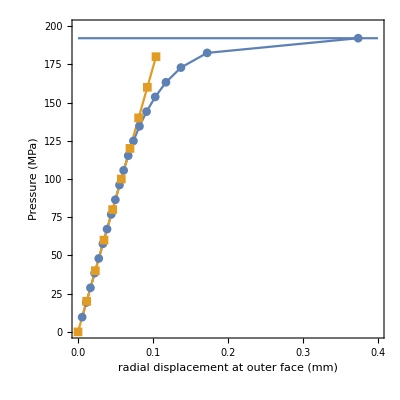

```mathematica
Show[cp,ListLinePlot[{outerdisplace,tab,cp},PlotRange->All,PlotMarkers->Automatic],Frame->True,FrameLabel->{"radial displacement at outer face (mm)","Pressure (MPa)"}]
```

```mathematica
soln=19;
plasticdefx=Table[{epspsolu[[soln]][[i]][[1]],epspsolu[[soln]][[i]][[2]],epspsolu[[soln]][[i]][[3]][[1]]},{i,1,Length[epspsolu[[soln]]]}];
plasticdefy=Table[{epspsolu[[soln]][[i]][[1]],epspsolu[[soln]][[i]][[2]],epspsolu[[soln]][[i]][[3]][[2]]},{i,1,Length[epspsolu[[soln]]]}];
plasticdefxy=Table[{epspsolu[[soln]][[i]][[1]],epspsolu[[soln]][[i]][[2]],epspsolu[[soln]][[i]][[3]][[3]]},{i,1,Length[epspsolu[[soln]]]}];


plasticstressx=Table[{stresssolu[[soln]][[i]][[1]],stresssolu[[soln]][[i]][[2]],stresssolu[[soln]][[i]][[3]][[1]]},{i,1,Length[stresssolu[[soln]]]}];
plasticstressy=Table[{stresssolu[[soln]][[i]][[1]],stresssolu[[soln]][[i]][[2]],stresssolu[[soln]][[i]][[3]][[2]]},{i,1,Length[stresssolu[[soln]]]}];
plasticstressxy=Table[{stresssolu[[soln]][[i]][[1]],stresssolu[[soln]][[i]][[2]],stresssolu[[soln]][[i]][[3]][[3]]},{i,1,Length[stresssolu[[soln]]]}];
size=Length[stresssolu[[soln]] ];
yieldfunc=Table[0,{size}];
Table[
x=stresssolu[[soln]][[i]][[1]];
y=stresssolu[[soln]][[i]][[2]];
sigx=stresssolu[[soln]][[i]][[3]][[1]];
sigyy=stresssolu[[soln]][[i]][[3]][[2]];
tauxy=stresssolu[[soln]][[i]][[3]][[3]];
If[planestress==True,
sigz=0;
,
sigz=nu(sigx+sigyy);
];

j2=1/3.(sigx^2+3. tauxy^2+sigyy^2-sigyy sigz+sigz^2-sigx (sigyy+sigz));
yieldfunc[[i]]={x,y,Sqrt[3 j2]-sigy};

,{i,1,size}];
EPBAR=Table[0,{size}];
Table[
x=epspsolu[[soln]][[i]][[1]];
y=epspsolu[[soln]][[i]][[2]];
EPPX=epspsolu[[soln]][[i]][[3]][[1]];
EPPY=epspsolu[[soln]][[i]][[3]][[2]];
EPPXY=epspsolu[[soln]][[i]][[3]][[2]];
EPBAR[[i]]={x,y,EPPX+EPPY+EPPXY};

,{i,1,size}];
```

```mathematica
size=Length[stresssolu[[soln]] ];
```

```mathematica
Length[stresssolu[[soln]]]
```

```mathematica
40+0.0228  12070
```

315.196

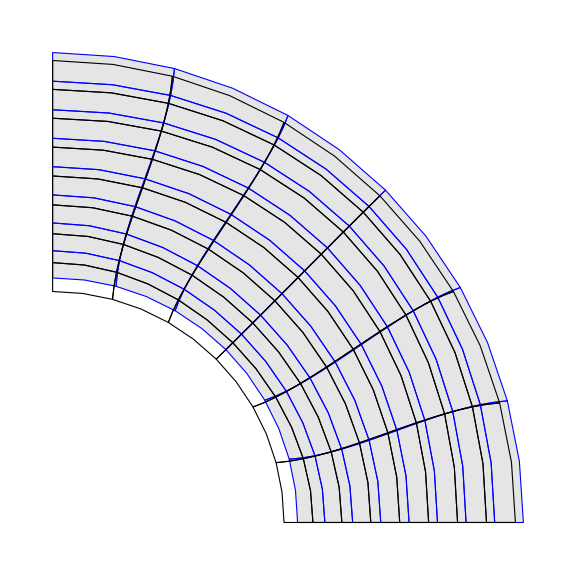

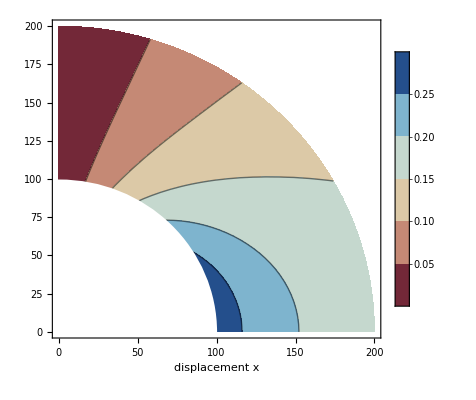

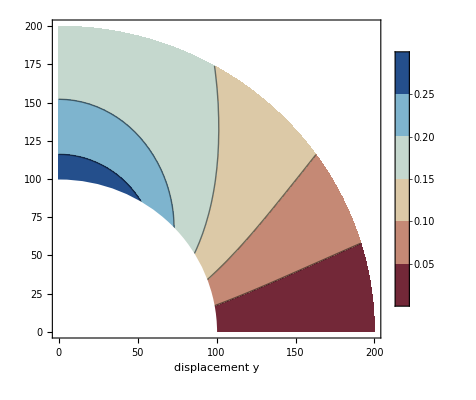

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
sol=solss[[soln]];
scale=20;
deformed=(Flatten[nnodes]+scale sol);
tabdeformed=ParallelTable[{ deformed[[i]], deformed[[i+1]]},{i,1,Length[deformed],2}];
meshVis1=Graphics[{FaceForm[],EdgeForm[{Dashed}],GraphicsComplex[nnodes,Polygon[topol[[All,{1,5,2,6,3,7,4,8}]]]]}];
meshVisDef=Graphics[{FaceForm[{Gray,Opacity[0.2]}],EdgeForm[Blue],GraphicsComplex[tabdeformed,Polygon[topol[[All,{1,5,2,6,3,7,4,8}]]]]}];
defplussundef=Show[meshVisDef,meshVis1,ImageSize->Large]


{sols,dsols,X}=ComputeSol[topol,nnodes,order,sol,eltype]//Simplify//Chop;
{stress,strain,stressz,J2,I1}=ComputeStress[dsols,young,nu];
lpd=Show[Graphics[{GrayLevel[1],Disk[{0,0},R]},AspectRatio->Automatic]];
(*tabux=computesollist[X,sols,1];*)
tabux=postproc[X,Transpose[sols][[1]]];
(*tabuy=computesollist[X,sols,2];*)
tabuy=postproc[X,Transpose[sols][[2]]];
(*tabsx=computesollist[X,stress,1];*)
tabsx=postproc[X,Transpose[stress][[1]]];
(*tabsy=computesollist[X,stress,2];*)
tabsy=postproc[X,Transpose[stress][[2]]];
(*tabsxy=computesollist[X,stress,3];*)
tabsxy=postproc[X,Transpose[stress][[3]]];
(*tabsJ2=computesollist2[X,J2,3];*)
tabsJ2=postproc[X,J2];
tabsI1=postproc[X,I1];
tabssz=postproc[X,stressz];



n=20;
maxnpts=300;
intoorder=20;
lpux=ListContourPlot[Flatten[tabux,1],ColorFunction->"RedBlueTones",Frame->True,FrameLabel->{"displacement x"},AspectRatio->Automatic,PlotLegends->Automatic];
lpuy=ListContourPlot[Flatten[tabuy,1],ColorFunction->"RedBlueTones",AspectRatio->Automatic,Frame->True, FrameLabel->{"displacement y"},PlotLegends->Automatic];

lpsJ2=ListContourPlot[Flatten[tabsJ2,1],ColorFunction->"RedBlueTones",AspectRatio->Automatic,PlotLegends->Automatic, Frame->True,FrameLabel->{"J2"},Contours->n,PerformanceGoal->"Quality"];
lpsI1=ListContourPlot[Flatten[tabsI1,1],ColorFunction->"RedBlueTones",AspectRatio->Automatic,PlotLegends->Automatic,Frame->True,FrameLabel->{"I1"},Contours->n,PerformanceGoal->"Quality"];
lpsstressz=ListContourPlot[Flatten[tabssz,1],ColorFunction->"RedBlueTones",Frame->True,FrameLabel->{"sigz"},AspectRatio->Automatic,PlotLegends->Automatic,Contours->n,PerformanceGoal->"Quality"];

lptabepx=ListContourPlot[plasticdefx,ColorFunction->"RedBlueTones",AspectRatio->Automatic,Frame->True,FrameLabel->{"epsPX"},PlotLegends->BarLegend[Automatic,All],Contours->n,PerformanceGoal->"Quality",MaxPlotPoints->maxnpts,InterpolationOrder->intoorder,PlotRange->{Min[Transpose[plasticdefx][[3]]],Max[Transpose[plasticdefx][[3]]]}];
lptabepy=ListContourPlot[plasticdefy,ColorFunction->"RedBlueTones",AspectRatio->Automatic,Frame->True,FrameLabel->{"epsPY"},PlotLegends->BarLegend[Automatic,All],Contours->n,PerformanceGoal->"Quality",MaxPlotPoints->maxnpts,InterpolationOrder->intoorder,PlotRange->{Min[Transpose[plasticdefy][[3]]],Max[Transpose[plasticdefy][[3]]]}];
lptabepxy=ListContourPlot[plasticdefxy,ColorFunction->"RedBlueTones",AspectRatio->Automatic,Frame->True,FrameLabel->{"epsPXY"},PlotLegends->BarLegend[Automatic,All],Contours->n,PerformanceGoal->"Quality",MaxPlotPoints->maxnpts,InterpolationOrder->intoorder,PlotRange->{Min[Transpose[plasticdefxy][[3]]],Max[Transpose[plasticdefxy][[3]]]}];

lpsx=ListContourPlot[plasticstressx,ColorFunction->"RedBlueTones",AspectRatio->Automatic,Frame->True,FrameLabel->{"SigX"},PlotLegends->BarLegend[Automatic,All],Contours->n,PerformanceGoal->"Quality",MaxPlotPoints->maxnpts,InterpolationOrder->intoorder,PlotRange->{Min[Transpose[plasticstressx][[3]]],Max[Transpose[plasticstressx][[3]]]}];
lpsy=ListContourPlot[plasticstressy,ColorFunction->"RedBlueTones",AspectRatio->Automatic,Frame->True,FrameLabel->{"SigY"},PlotLegends->BarLegend[Automatic,All],Contours->n,PerformanceGoal->"Quality",MaxPlotPoints->maxnpts,InterpolationOrder->intoorder,PlotRange->{Min[Transpose[plasticstressy][[3]]],Max[Transpose[plasticstressy][[3]]]}];
lpsxy=ListContourPlot[plasticstressxy,ColorFunction->"RedBlueTones",AspectRatio->Automatic,Frame->True,FrameLabel->{"SigXY"},PlotLegends->BarLegend[Automatic,All],Contours->n,PerformanceGoal->"Quality",MaxPlotPoints->maxnpts,InterpolationOrder->intoorder,PlotRange->{Min[Transpose[plasticstressxy][[3]]],Max[Transpose[plasticstressxy][[3]]]}];

yield=ListContourPlot[yieldfunc,ColorFunction->"RedBlueTones",AspectRatio->Automatic,Frame->True,FrameLabel->{"yield func"},PlotLegends->BarLegend[Automatic,All],Contours->n,PerformanceGoal->"Quality",MaxPlotPoints->maxnpts,InterpolationOrder->intoorder,PlotRange->{Min[Transpose[yieldfunc][[3]]],Max[Transpose[yieldfunc][[3]]]}];

epbar=ListContourPlot[EPBAR,ColorFunction->"RedBlueTones",AspectRatio->Automatic,Frame->True,FrameLabel->{"EPBAR"},PlotLegends->BarLegend[Automatic,All],Contours->n,PerformanceGoal->"Quality",MaxPlotPoints->maxnpts,InterpolationOrder->intoorder,PlotRange->{Min[Transpose[EPBAR][[3]]],Max[Transpose[EPBAR][[3]]]}];




Show[lpux,lpd]
Show[lpuy,lpd]

Show[lpsx,lpd]
Show[lpsy,lpd]
Show[lpsxy,lpd]

Show[lptabepx,lpd]
Show[lptabepy,lpd]
Show[lptabepxy,lpd]

Show[lpsJ2,lpd]
Show[lpsI1,lpd]
Show[yield,lpd]
Show[epbar,lpd]
```